# Notebook for : 300 Problems in Special and General Relativity by Blennow and Ohlsson

Geoff Cope
University of Utah
                                                                                                             𐐏𐐭𐑌𐐲𐑂𐐲𐑉𐑅𐐮𐐻𐐨 𐐲𐑂 𐐏𐐭𐐻𐐫
February 22, 2023

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

## Hyperlink To Book

```mathematica
Hyperlink["300 Problems in Special and General Relativity by Blennow and Ohlsson",
"https://www.cambridge.org/core/books/300-problems-in-special-and-general-relativity/9CF1D0B340CBD91F2279F5EC054DF900"]
```

[300 Problems in Special and General Relativity by Blennow and Ohlsson](https://www.cambridge.org/core/books/300-problems-in-special-and-general-relativity/9CF1D0B340CBD91F2279F5EC054DF900)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 627 Kb

{Utilities`CleanSlate`,GeneralRelativityTensors`,Notation`,VariationalMethods`,GeneralRelativityTensors`CommonTensors`,GeneralRelativityTensors`TensorDerivatives`,GeneralRelativityTensors`TensorManipulation`,GeneralRelativityTensors`TensorDefinitions`,GeneralRelativityTensors`Utils`,DocumentationSearch`,ResourceLocator`,NaturalLanguageProcessingLoader`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

```mathematica
Needs["VariationalMethods`"]
```

## Custom Notation

```mathematica
<<Notation`
```

```mathematica
CreatePalette[{ 
PasteButton[SubPlus[β]] , 
PasteButton[SubMinus[β]]  , 
PasteButton[Subscript[r,s]],
PasteButton[SubPlus[r]] , 
PasteButton[SubMinus[r]]  
}]
```

wuggr_shm37FrontEndObject[LinkObject["wuggr_shm", 3, 1]]37Untitled-3

```mathematica
Symbolize[β_+]
Symbolize[β_-]
Symbolize[Subscript[r, s]]
Symbolize[r_+]
Symbolize[r_-]
```

```mathematica
Clear[dtReplace]
dtReplace = {
Dt[r]-> dr ,
Dt[s]-> ds ,  
Dt[t]-> dt , 
Dt[u]-> du , 
Dt[v]-> dv ,
Dt[x]-> dx , 
Dt[y]-> dy , 
Dt[z]-> dz ,  
 Dt[θ] -> dθ , 
Dt[ϕ] -> dϕ  ,
Dt[η] -> dη  , 
Dt[χ]-> dχ , 
Dt[ρ] -> dρ ,
Dt[φ] -> dφ , 
 Dt[𝓉] -> d𝓉 , 
Dt[𝓏] -> d𝓏,
Dt[T]-> dT , 
Dt[U]-> dU , 
Dt[V]-> dV ,
Dt[X]-> dX , 
Dt[Y]->  dY , 
Dt[Z]-> dZ , 
Dt[𝓇]-> d𝓇  , 
Dt[Φ]-> dΦ};
dtReplace // TableForm
```

Dt[r]→dr
Dt[s]→ds
Dt[t]→dt
Dt[u]→du
Dt[v]→dv
Dt[x]→dx
Dt[y]→dy
Dt[z]→dz
Dt[θ]→dθ
Dt[ϕ]→dϕ
Dt[η]→dη
Dt[χ]→dχ
Dt[ρ]→dρ
Dt[φ]→dφ
Dt[𝓉]→d𝓉
Dt[𝓏]→d𝓏
Dt[T]→dT
Dt[U]→dU
Dt[V]→dV
Dt[X]→dX
Dt[Y]→dY
Dt[Z]→dZ
Dt[𝓇]→d𝓇
Dt[Φ]→dΦ

```mathematica
M /: Dt[M] = 0 ;  (* Mass of Schwarzschild is constant *) (* We use M for mass and m for null vector *) 
Subscript[r, s] /: Dt[Subscript[r, s]] = 0 ;
a /: Dt[a] = 0 ;  (* a^2 is usually x^2+y^2+z^2== a^2 so we treat a as some constant *)
K /: Dt[K] = 0 ; (* Problem 2.21 Pages 46 and 203 *)
```

## Line Element and Metric Functions

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[metricToLine]
metricToLine[metric_, differentials_]:= 
Sum[metric[[i,j]] differentials[[i]] differentials[[j]] , {i,1,Length[differentials]},{j,1,Length[differentials]}]
```

## Indexed Tensors Equation 0.6 and 0.7 (Redo this.... on the right track...)

```mathematica
(* Here we use the letter "O" and NOT the number "0" *) 

Clear[variables]
variables = 
{1,2,3,4}
```

{1,2,3,4}

```mathematica
Table[Subscript[𝒜,ToExpression[StringJoin[ToString[variables[[i]]],ToString[variables[[j]]]]]],{i,1,4},{j,1,4}] // MatrixForm
```

(𝒜_11 | 𝒜_12 | 𝒜_13 | 𝒜_14
𝒜_21 | 𝒜_22 | 𝒜_23 | 𝒜_24
𝒜_31 | 𝒜_32 | 𝒜_33 | 𝒜_34
𝒜_41 | 𝒜_42 | 𝒜_43 | 𝒜_44)

```mathematica
Table[ Subsuperscript[𝒜,ToExpression[StringJoin[ToString[variables[[i]]],ToString[variables[[j]]]]],i],{i,1,4},{j,1,4}]  // MatrixForm
```

(𝒜_11^1 | 𝒜_12^1 | 𝒜_13^1 | 𝒜_14^1
𝒜_21^2 | 𝒜_22^2 | 𝒜_23^2 | 𝒜_24^2
𝒜_31^3 | 𝒜_32^3 | 𝒜_33^3 | 𝒜_34^3
𝒜_41^4 | 𝒜_42^4 | 𝒜_43^4 | 𝒜_44^4)

## Minkowski Metric Defined as a Tensor Equation 0.8 (Used for raising, lowering, and contractions)

```mathematica
Clear[eq0pt8]
eq0pt8 = 
c^2 dt^2 - dx^2-dy^2-dz^2
```

c^2 dt^2-dx^2-dy^2-dz^2

```mathematica
Clear[minkowskiMetric]
minkowskiMetric = 
lineToMetric[eq0pt8,{dt,dx,dy,dz}]  ;
minkowskiMetric // MatrixForm
```

(c^2 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

```mathematica
Clear[gMinkowski ]
gMinkowski  = 
ToMetric["gminkowski", {t,x,y,z} ,minkowskiMetric ,  "Greek"]
```

gminkowski_αβ^

```mathematica
gMinkowski[-μ,-ν]

TensorValues[gMinkowski[-μ,-ν]] // MatrixForm
```

gminkowski_μν^

(c^2 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

## Λ Matrices Equation 0.14 Page 4

```mathematica
Clear[eq0pt14]
eq0pt14 = {
Λ == ({{Cosh[θ], -Sinh[θ], 0, 0}, {-Sinh[θ], Cosh[θ], 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}}) , 
Λ == ({{γ, -β γ, 0, 0}, {-β γ, γ, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}})
} ;
eq0pt14[[1]][[2]] // MatrixForm
eq0pt14[[2]][[2]] // MatrixForm
```

(Cosh[θ] | -Sinh[θ] | 0 | 0
-Sinh[θ] | Cosh[θ] | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

(γ | -β γ | 0 | 0
-β γ | γ | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
(* Find way to get rid of minus sign *) 

Clear[coshSinhGammaBeta]
coshSinhGammaBeta = 
DeleteDuplicates[DeleteCases[  Thread[Flatten[eq0pt14[[1]][[2]]]== Flatten[eq0pt14[[2]][[2]]] ] ,True] ] ;
coshSinhGammaBeta// TableForm
```

Cosh[θ]==γ
-Sinh[θ]==-β γ

```mathematica
Clear[coshSinhTanhReplace]
coshSinhTanhReplace = { 
Cosh[θ]:> γ  , 
Sinh[θ]:> β γ , 
Tanh[θ]:> β 
} ;
coshSinhTanhReplace  // TableForm
```

Cosh[θ]:>γ
Sinh[θ]:>β γ
Tanh[θ]:>β

```mathematica
Clear[eq0pt15]
eq0pt15 = 
Flatten[Solve[coshSinhGammaBeta,{γ,β} ]] /. Rule-> Equal   ;
eq0pt15// TableForm
```

γ==Cosh[θ]
β==Tanh[θ]

```mathematica
Clear[eq0pt15a]
eq0pt15a  = 
MultiplySides[eq0pt15[[1]],eq0pt15[[2]]]
```

β γ==Sinh[θ]

```mathematica
Clear[gammaBetaDefintions]
gammaBetaDefintions = {
γ == 1/(√(1 - v^2/c^2)) , 
β == v/c , 
γ == 1/(√(1 -β^2))

}   ;
gammaBetaDefintions  // TableForm
```

γ==1/(√(1-v^2/c^2))
β==v/c
γ==1/(√(1-β^2))

## Faraday Tensor Convention Equation 0.25 Page 5

```mathematica
Clear[eq0pt25]
eq0pt25 = 
ℱ == ({{0, -E1, -E2, -E3}, {E1, 0, -c B3, c B2}, {E2, c B3, 0, -c B1}, {E3, -c B2, c B1, 0}}) ;
eq0pt25[[2]] // MatrixForm
```

(0 | -E1 | -E2 | -E3
E1 | 0 | -B3 c | B2 c
E2 | B3 c | 0 | -B1 c
E3 | -B2 c | B1 c | 0)

```mathematica
(* We'll use this notation for a transformed ℱ so we can equate components... *) 

Clear[eq0pt25a]
eq0pt25a = 
ℱ == ({{0, -ℰ1, -ℰ2, -ℰ3}, {ℰ1, 0, -c ℬ3, c ℬ2}, {ℰ2, c ℬ3, 0, -c ℬ1}, {ℰ3, -c ℬ2, c ℬ1, 0}})  ;
eq0pt25a[[2]] // MatrixForm
```

(0 | -ℰ1 | -ℰ2 | -ℰ3
ℰ1 | 0 | -c ℬ3 | c ℬ2
ℰ2 | c ℬ3 | 0 | -c ℬ1
ℰ3 | -c ℬ2 | c ℬ1 | 0)

## Problem 1.34 Page 21 and 98

```mathematica
(* We'll call these the primed indices using [esc]scx[esc] for 𝓍 instead of x' *) 
(* For double prime we'll just use capital X *) 
(* We'll use [esc]ctheta[esc] for ϑ - second angle *) 

Table[Superscript[x,i],{i,0,3}]
Table[Superscript[𝓍,i],{i,0,3}]
Table[Superscript[X,i],{i,0,3}]
eq0pt14[[1]][[2]] // MatrixForm
( eq0pt14[[1]][[2]]  /. θ-> ϑ ) // MatrixForm
( eq0pt14[[1]][[2]]  /. θ-> Θ ) // MatrixForm (* Hard to read but this is capital theta and we'll use this for theta double prime *)
```

{x^0,x^1,x^2,x^3}

{𝓍^0,𝓍^1,𝓍^2,𝓍^3}

{X^0,X^1,X^2,X^3}

(Cosh[θ] | -Sinh[θ] | 0 | 0
-Sinh[θ] | Cosh[θ] | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

(Cosh[ϑ] | -Sinh[ϑ] | 0 | 0
-Sinh[ϑ] | Cosh[ϑ] | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

(Cosh[Θ] | -Sinh[Θ] | 0 | 0
-Sinh[Θ] | Cosh[Θ] | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
Clear[firstTransformation]
firstTransformation = 
Thread[Table[Superscript[𝓍,i],{i,0,3}]== ( eq0pt14[[1]][[2]] . Table[Superscript[x,i],{i,0,3}] )  ]  ;
firstTransformation// TableForm
```

𝓍^0==Cosh[θ] x^0-Sinh[θ] x^1
𝓍^1==-Sinh[θ] x^0+Cosh[θ] x^1
𝓍^2==x^2
𝓍^3==x^3

```mathematica
Clear[secondTransformation]
secondTransformation = 
Thread[Table[Superscript[X,i],{i,0,3}]== ( eq0pt14[[1]][[2]]  /. θ-> ϑ ) . Table[Superscript[𝓍,i],{i,0,3}]]  ;
secondTransformation//TableForm
```

X^0==Cosh[ϑ] 𝓍^0-Sinh[ϑ] 𝓍^1
X^1==-Sinh[ϑ] 𝓍^0+Cosh[ϑ] 𝓍^1
X^2==𝓍^2
X^3==𝓍^3

```mathematica
ApplySides[Simplify, ( secondTransformation /. ( firstTransformation /. Equal-> Rule  )  )] // TableForm
```

X^0==Cosh[θ+ϑ] x^0-Sinh[θ+ϑ] x^1
X^1==-Sinh[θ+ϑ] x^0+Cosh[θ+ϑ] x^1
X^2==x^2
X^3==x^3

## Problem 1.40 Pages 22 and 103

```mathematica
Clear[eq3pt157]
eq3pt157 = 
γ * Join[{1},Table[Superscript[v,i],{i,1,3}]]
```

{γ,γ v^1,γ v^2,γ v^3}

```mathematica
Clear[eq3pt159,u]
eq3pt159 = 
Λ == ({{γ, 0, -u *γ, 0}, {0, 1, 0, 0}, {-u *γ, 0, γ, 0}, {0, 0, 0, 1}}) ;
eq3pt159[[2]] // MatrixForm // pdConv
```

(γ | 0 | γ (-u) | 0
0 | 1 | 0 | 0
γ (-u) | 0 | γ | 0
0 | 0 | 0 | 1)

```mathematica
(* redo this.... there's a gamma of u and a gamma of v ... be careful... *) 

Clear[eq3pt160]
eq3pt160 = 
Collect[Table[Sum[eq3pt159[[2]][[μ,ν]]eq3pt157[[ν]],{ν,1,4}],{μ,1,4}],γ^2] ;
eq3pt160  // TableForm
```

γ^2 (1-u v^2)
γ v^1
γ^2 (-u+v^2)
γ v^3

## Problem 1.127 Page 38

```mathematica
Clear[p1pt127]
p1pt127 = { 
Flatten[{Thread[{E1,E2,E3}-> {α,0,0}] ,Thread[{B1,B2,B3}-> {α/c,0,(2α)/c}]  } ],
Flatten[{Thread[{E1,E2,E3}-> {Ex,α,0}] ,Thread[{B1,B2,B3}-> {α/c,By,α/c}]  } ]
} ;
p1pt127[[1]]
p1pt127[[2]]
```

{E1→α,E2→0,E3→0,B1→α/c,B2→0,B3→(2 α)/c}

{E1→Ex,E2→α,E3→0,B1→α/c,B2→By,B3→α/c}

```mathematica
eq0pt25[[2]] // MatrixForm
eq0pt14[[2]][[2]] // MatrixForm
```

(0 | -E1 | -E2 | -E3
E1 | 0 | -B3 c | B2 c
E2 | B3 c | 0 | -B1 c
E3 | -B2 c | B1 c | 0)

(γ | -β γ | 0 | 0
-β γ | γ | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

## Problem 1.140 Page 40

```mathematica
Clear[eq1pt140]
eq1pt140 = 
ℰ == (d/(4 π ϵ)){(3 x z)/r^5 , (3 y z)/r^5 , (3 z^2 - r^2)/r^5}
```

ℰ=={(3 d x z)/(4 π r^5 ϵ),(3 d y z)/(4 π r^5 ϵ),(d (-r^2+3 z^2))/(4 π r^5 ϵ)}

```mathematica
Thread[{E1,E2,E3}-> eq1pt140[[2]] ] // TableForm
Thread[{B1,B2,B3}->{0,0,0} ]  // TableForm
```

E1→(3 d x z)/(4 π r^5 ϵ)
E2→(3 d y z)/(4 π r^5 ϵ)
E3→(d (-r^2+3 z^2))/(4 π r^5 ϵ)

B1→0
B2→0
B3→0

```mathematica
Clear[faradayTensor1pt140]
faradayTensor1pt140 = 
eq0pt25[[2]] /. Thread[{E1,E2,E3}-> eq1pt140[[2]] ] /. Thread[{B1,B2,B3}->{0,0,0} ] ;
faradayTensor1pt140  // MatrixForm
```

(0 | -(3 d x z)/(4 π r^5 ϵ) | -(3 d y z)/(4 π r^5 ϵ) | -(d (-r^2+3 z^2))/(4 π r^5 ϵ)
(3 d x z)/(4 π r^5 ϵ) | 0 | 0 | 0
(3 d y z)/(4 π r^5 ϵ) | 0 | 0 | 0
(d (-r^2+3 z^2))/(4 π r^5 ϵ) | 0 | 0 | 0)

```mathematica
(* Here we'll use the LeviCivitaTensor and see if this works... [esc]ce[esc] for ε *) 

Clear[ε]
ε = 
LeviCivitaTensor[4]
```

SparseArray[…]

```mathematica
(* Happy accident... we get zero... no idea if this was the right way to do it... *) 

Clear[eq3pt370]
eq3pt370 = 
Sum[ ε[[μ,ν,σ,ρ]]faradayTensor1pt140[[μ,ν]]faradayTensor1pt140[[σ,ρ]] , {μ,1,4},{ν,1,4},{σ,1,4},{ρ,1,4}]
```

0

## Line Element and Metric 2.116 (Page 67)

```mathematica
(* Here we use [esc]scr[esc] instead of r_* *) 

Clear[p2pt116]
p2pt116 = 
(1-𝓇/r) dt^2- (1-𝓇/r)^-1 dr^2-r^2( dθ^2+ Sin[θ]^2 dϕ^2)
```

-dr^2/(1-𝓇/r)+dt^2 (1-𝓇/r)-r^2 (dθ^2+dϕ^2 Sin[θ]^2)

```mathematica
Clear[metric2pt116]
metric2pt116 = 
lineToMetric[p2pt116,{dt,dr,dθ,dϕ}]  ;
metric2pt116 // MatrixForm // pdConv
```

(1-𝓇/r | 0 | 0 | 0
0 | -1/(1-𝓇/r) | 0 | 0
0 | 0 | -r^2 | 0
0 | 0 | 0 | -r^2 sin^2(θ))

## Calculation of Tensors Associated With Metric 2.116 (Page 67)

```mathematica
Clear[input2pt116] 
input2pt116[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList2pt116];
tensorList2pt116 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList2pt116[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList2pt116[[2]]  = 
ChristoffelSymbol[ tensorList2pt116[[1]] , ActWith-> Simplify] ;
tensorList2pt116[[3]] = 
RiemannTensor[ tensorList2pt116[[1]] , ActWithNested-> Simplify ];
tensorList2pt116[[4]] = 
RicciTensor[ tensorList2pt116[[1]] , ActWith-> Simplify ] ;
tensorList2pt116[[5]] = 
RicciScalar[ tensorList2pt116[[1]] , ActWith-> Simplify ] ;
tensorList2pt116[[6]] = 
KretschmannScalar[ tensorList2pt116[[1]] , ActWith-> Simplify] ; 
tensorList2pt116[[7]] = 
EinsteinTensor[ tensorList2pt116[[1]] , ActWith-> Simplify] ;  
tensorList2pt116[[8]] = 
WeylTensor[ tensorList2pt116[[1]] , ActWith-> Simplify ] ;
 tensorList2pt116[[9]] = 
CottonTensor[ tensorList2pt116[[1]] , ActWith-> Simplify ] ; 
];
```

```mathematica
(* Last timing took 9.08 for all tensors *) 
input2pt116[ "metric2pt116", metric2pt116, "Schwarzschild","g^schw",{t,r,θ,ϕ}, "Greek"] // Timing
```

Indices must be a list of Symbols (and negative Symbols).

Aborting in ToTensor[].

$Aborted

```mathematica
tensorList2pt116
```

{gmetric2pt116,christoffelmetric2pt116,riemannmetric2pt116,riccimetric2pt116,ricciscalarmetric2pt116,kretschmannscalarmetric2pt116,einsteinmetric2pt116,weylmetric2pt116,cottonmetric2pt116}

```mathematica
tensorList2pt116[[1]] 
TensorName[tensorList2pt116[[1]]] 
TensorValues[tensorList2pt116[[1]]] // MatrixForm // pdConv
```

gmetric2pt116

Invalid call to TensorName[]. Unexpected parameters: {gmetric2pt116}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {gmetric2pt116}

$Aborted

```mathematica
tensorList2pt116[[2]] 
TensorName[tensorList2pt116[[2]]] 
TensorValues[tensorList2pt116[[2]]] // MatrixForm // pdConv
```

christoffelmetric2pt116

Invalid call to TensorName[]. Unexpected parameters: {christoffelmetric2pt116}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {christoffelmetric2pt116}

$Aborted

```mathematica
tensorList2pt116[[3]] 
TensorName[tensorList2pt116[[3]]] 
TensorValues[tensorList2pt116[[3]]] // MatrixForm // pdConv
```

riemannmetric2pt116

Invalid call to TensorName[]. Unexpected parameters: {riemannmetric2pt116}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {riemannmetric2pt116}

$Aborted

```mathematica
tensorList2pt116[[4]] 
TensorName[tensorList2pt116[[4]]] 
TensorValues[tensorList2pt116[[4]]] // MatrixForm // pdConv
```

riccimetric2pt116

Invalid call to TensorName[]. Unexpected parameters: {riccimetric2pt116}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {riccimetric2pt116}

$Aborted

```mathematica
tensorList2pt116[[5]] 
TensorName[tensorList2pt116[[5]]] 
TensorValues[tensorList2pt116[[5]]] // MatrixForm // pdConv
```

ricciscalarmetric2pt116

Invalid call to TensorName[]. Unexpected parameters: {ricciscalarmetric2pt116}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {ricciscalarmetric2pt116}

$Aborted

```mathematica
tensorList2pt116[[6]] 
TensorName[tensorList2pt116[[6]]] 
TensorValues[tensorList2pt116[[6]]] // MatrixForm // pdConv
```

kretschmannscalarmetric2pt116

Invalid call to TensorName[]. Unexpected parameters: {kretschmannscalarmetric2pt116}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {kretschmannscalarmetric2pt116}

$Aborted

```mathematica
tensorList2pt116[[7]] 
TensorName[tensorList2pt116[[7]]] 
TensorValues[tensorList2pt116[[7]]] // MatrixForm // pdConv
```

einsteinmetric2pt116

Invalid call to TensorName[]. Unexpected parameters: {einsteinmetric2pt116}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {einsteinmetric2pt116}

$Aborted

```mathematica
tensorList2pt116[[8]] 
TensorName[tensorList2pt116[[8]]] 
TensorValues[tensorList2pt116[[8]]] // MatrixForm // pdConv
```

weylmetric2pt116

Invalid call to TensorName[]. Unexpected parameters: {weylmetric2pt116}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {weylmetric2pt116}

$Aborted

```mathematica
tensorList2pt116[[9]] 
TensorName[tensorList2pt116[[9]]] 
TensorValues[tensorList2pt116[[9]]] // MatrixForm // pdConv
```

cottonmetric2pt116

Invalid call to TensorName[]. Unexpected parameters: {cottonmetric2pt116}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {cottonmetric2pt116}

$Aborted

## Kretschmann For Metric 2.116 (Different by a constant factor)

```mathematica
(* Our invariant has a factor of 12, theirs has a 3... probably a two floating around from metric somewhere... *) 

tensorList2pt116[[6]] 
TensorName[tensorList2pt116[[6]]] 

Clear[eq2pt117]
eq2pt117 = 
TensorValues[tensorList2pt116[[6]]]
```

kretschmannscalarmetric2pt116

Invalid call to TensorName[]. Unexpected parameters: {kretschmannscalarmetric2pt116}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {kretschmannscalarmetric2pt116}

$Aborted

## Line Element and Metric 2.118 (Page 69)

```mathematica
(* signature of metric - make sure to get this right... *) 
(* also - this form of the metric is changed in answer... *)

Clear[p2pt118]
p2pt118 = 
(1 + 2 Φ[r] ) dt^2-(1 +2 Φ[r] )^-1 dr^2- r^2 ( dθ^2+ Sin[θ]^2 dϕ^2)
```

-r^2 (dθ^2+dϕ^2 Sin[θ]^2)-dr^2/(1+2 Φ[r])+dt^2 (1+2 Φ[r])

```mathematica
Clear[metric2pt118]
metric2pt118 = 
lineToMetric[p2pt118 ,{dt,dr,dθ,dϕ}] ;
metric2pt118// MatrixForm // pdConv
```

(2 Φ(r)+1 | 0 | 0 | 0
0 | -1/(2 Φ(r)+1) | 0 | 0
0 | 0 | -r^2 | 0
0 | 0 | 0 | -r^2 sin^2(θ))

```mathematica
Clear[p2pt118a]
p2pt118a = 
Φ[r] == -((G M)/r)
```

Φ[r]==-(G M)/r

```mathematica
Clear[phiDerivartives]
phiDerivartives = { 
p2pt118a  , 
D[p2pt118a ,r] , 
D[p2pt118a ,{r,2}]
} /. Equal-> Rule ;
phiDerivartives  // TableForm
```

Φ[r]→-(G M)/r
Φ'[r]→(G M)/r^2
Φ''[r]→-(2 G M)/r^3

## Calculation of Tensors Associated With Metric 2.118

```mathematica
Clear[input2pt118] 
input2pt118[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList2pt118];
tensorList2pt118 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList2pt118[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList2pt118[[2]]  = 
ChristoffelSymbol[ tensorList2pt118[[1]] , ActWith-> Simplify] ;
tensorList2pt118[[3]] = 
RiemannTensor[ tensorList2pt118[[1]] , ActWithNested-> Simplify ];
tensorList2pt118[[4]] = 
RicciTensor[ tensorList2pt118[[1]] , ActWith-> Simplify ] ;
tensorList2pt118[[5]] = 
RicciScalar[ tensorList2pt118[[1]] , ActWith-> Simplify ] ;
tensorList2pt118[[6]] = 
KretschmannScalar[ tensorList2pt118[[1]] , ActWith-> Simplify] ; 
tensorList2pt118[[7]] = 
EinsteinTensor[ tensorList2pt118[[1]] , ActWith-> Simplify] ;  
tensorList2pt118[[8]] = 
WeylTensor[ tensorList2pt118[[1]] , ActWith-> Simplify ] ;
 tensorList2pt118[[9]] = 
CottonTensor[ tensorList2pt118[[1]] , ActWith-> Simplify ] ; 
];
```

```mathematica
(* Last timing took 9.08 for all tensors *) 
input2pt118[ "metric2pt118", metric2pt118, "Newtonian","g^newt",{t,r,θ,ϕ}, "Greek"] // Timing
```

Indices must be a list of Symbols (and negative Symbols).

Aborting in ToTensor[].

$Aborted

```mathematica
tensorList2pt118
```

{gmetric2pt118,christoffelmetric2pt118,riemannmetric2pt118,riccimetric2pt118,ricciscalarmetric2pt118,kretschmannscalarmetric2pt118,einsteinmetric2pt118,weylmetric2pt118,cottonmetric2pt118}

```mathematica
tensorList2pt118[[1]] 
TensorName[tensorList2pt118[[1]]] 
TensorValues[tensorList2pt118[[1]]] // MatrixForm // pdConv
```

gmetric2pt118

Invalid call to TensorName[]. Unexpected parameters: {gmetric2pt118}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {gmetric2pt118}

$Aborted

```mathematica
tensorList2pt118[[2]] 
TensorName[tensorList2pt118[[2]]] 
TensorValues[tensorList2pt118[[2]]] // MatrixForm // pdConv
```

christoffelmetric2pt118

Invalid call to TensorName[]. Unexpected parameters: {christoffelmetric2pt118}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {christoffelmetric2pt118}

$Aborted

```mathematica
tensorList2pt118[[3]] 
TensorName[tensorList2pt118[[3]]] 
TensorValues[tensorList2pt118[[3]]] // MatrixForm // pdConv
```

riemannmetric2pt118

Invalid call to TensorName[]. Unexpected parameters: {riemannmetric2pt118}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {riemannmetric2pt118}

$Aborted

```mathematica
tensorList2pt118[[4]] 
TensorName[tensorList2pt118[[4]]] 
TensorValues[tensorList2pt118[[4]]] // MatrixForm // pdConv
```

riccimetric2pt118

Invalid call to TensorName[]. Unexpected parameters: {riccimetric2pt118}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {riccimetric2pt118}

$Aborted

```mathematica
tensorList2pt118[[5]] 
TensorName[tensorList2pt118[[5]]] 
TensorValues[tensorList2pt118[[5]]] // MatrixForm // pdConv
```

ricciscalarmetric2pt118

Invalid call to TensorName[]. Unexpected parameters: {ricciscalarmetric2pt118}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {ricciscalarmetric2pt118}

$Aborted

```mathematica
tensorList2pt118[[6]] 
TensorName[tensorList2pt118[[6]]] 
TensorValues[tensorList2pt118[[6]]] // MatrixForm // pdConv
```

kretschmannscalarmetric2pt118

Invalid call to TensorName[]. Unexpected parameters: {kretschmannscalarmetric2pt118}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {kretschmannscalarmetric2pt118}

$Aborted

```mathematica
tensorList2pt118[[7]] 
TensorName[tensorList2pt118[[7]]] 
TensorValues[tensorList2pt118[[7]]] // MatrixForm // pdConv
```

einsteinmetric2pt118

Invalid call to TensorName[]. Unexpected parameters: {einsteinmetric2pt118}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {einsteinmetric2pt118}

$Aborted

```mathematica
tensorList2pt118[[8]] 
TensorName[tensorList2pt118[[8]]] 
TensorValues[tensorList2pt118[[8]]] // MatrixForm // pdConv
```

weylmetric2pt118

Invalid call to TensorName[]. Unexpected parameters: {weylmetric2pt118}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {weylmetric2pt118}

$Aborted

```mathematica
tensorList2pt118[[9]] 
TensorName[tensorList2pt118[[9]]] 
TensorValues[tensorList2pt118[[9]]] // MatrixForm // pdConv
```

cottonmetric2pt118

Invalid call to TensorName[]. Unexpected parameters: {cottonmetric2pt118}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {cottonmetric2pt118}

$Aborted

## Euler Lagrange Equations Giving Geodesic Equations For Metric 2.118 (Equations 3.1849 - 3.1851 Page 318 ) (Redo this.... this has been a disaster)

```mathematica
Clear[eulerLagrangeEquations]
eulerLagrangeEquations[metric_, variables_ , parameter_ ]:= Module[
{qReplace,eqs,eulerEquations} ,
 
Clear[q] ;
q = 
Flatten[Table[Map[variables[[i]],{parameter}] , {i,1,Length[variables]}]] ;

Clear[qReplace] ;
qReplace = 
Thread[variables -> q ] ;

Clear[ℒ] ;
ℒ = 
Sum[(metric /. qReplace)[[i,j]] *   D[q,parameter][[i]] D[q,parameter][[j]] , {i,1, Length[q]},{j,1,Length[q]}] ;

Clear[eqs] ;
eqs = 
Table[(D[ D[ ℒ ,  D[q[[i]], parameter]] , parameter ] -D[ ℒ ,  q[[i]]] )==0  , {i,1,Length[q]}] // Expand   ;

Clear[eulerEquations] ;
eulerEquations = 
Flatten[Solve[ eqs , D[q,{parameter,2}]] ] /. Rule-> Equal 

];
```

```mathematica
(* 
To get rid of the functional dependence on λ after computing the geodesic equations try useing this:

/.q_[λ] :> q 

*)
```

```mathematica
Clear[geodesicEquationsMetric2pt118]
geodesicEquationsMetric2pt118 =
eulerLagrangeEquations[metric2pt118,{t,r,θ,ϕ},τ]  // Expand ;
geodesicEquationsMetric2pt118 // TableForm
```

t''[τ]==-(2 r'[τ] t'[τ] Φ'[r[τ]])/(1+2 Φ[r[τ]])
r''[τ]==r[τ] θ'[τ]^2+2 r[τ] Φ[r[τ]] θ'[τ]^2+r[τ] Sin[θ[τ]]^2 ϕ'[τ]^2+2 r[τ] Sin[θ[τ]]^2 Φ[r[τ]] ϕ'[τ]^2+(r'[τ]^2 Φ'[r[τ]])/(1+2 Φ[r[τ]])^2+(2 Φ[r[τ]] r'[τ]^2 Φ'[r[τ]])/(1+2 Φ[r[τ]])^2-t'[τ]^2 Φ'[r[τ]]-2 Φ[r[τ]] t'[τ]^2 Φ'[r[τ]]
θ''[τ]==-(2 r'[τ] θ'[τ])/r[τ]+Cos[θ[τ]] Sin[θ[τ]] ϕ'[τ]^2
ϕ''[τ]==-(2 r'[τ] ϕ'[τ])/r[τ]-2 Cot[θ[τ]] θ'[τ] ϕ'[τ]

```mathematica
Clear[geodesicEquationsMetric2pt118Reduced]
geodesicEquationsMetric2pt118Reduced = 
geodesicEquationsMetric2pt118 /. q_[τ] :> q ;
geodesicEquationsMetric2pt118Reduced  // TableForm
```

t''==-(2 r' t' Φ'[r])/(1+2 Φ[r])
r''==r (θ')^2+2 r Φ[r] (θ')^2+r Sin[θ]^2 (ϕ')^2+2 r Sin[θ]^2 Φ[r] (ϕ')^2+((r')^2 Φ'[r])/(1+2 Φ[r])^2+(2 Φ[r] (r')^2 Φ'[r])/(1+2 Φ[r])^2-(t')^2 Φ'[r]-2 Φ[r] (t')^2 Φ'[r]
θ''==-(2 r' θ')/r+Cos[θ] Sin[θ] (ϕ')^2
ϕ''==-(2 r' ϕ')/r-2 Cot[θ] θ' ϕ'

```mathematica
Clear[firstIntegrals2pt118 ]
firstIntegrals2pt118  = 
FirstIntegrals[ ℒ , q , τ ]   ;
firstIntegrals2pt118 // TableForm
```

FirstIntegral[t]→-2 (1+2 Φ[r[τ]]) t'[τ]
FirstIntegral[ϕ]→2 r[τ]^2 Sin[θ[τ]]^2 ϕ'[τ]
FirstIntegral[τ]→-r'[τ]^2/(1+2 Φ[r[τ]])+(1+2 Φ[r[τ]]) t'[τ]^2-r[τ]^2 (θ'[τ]^2+Sin[θ[τ]]^2 ϕ'[τ]^2)

```mathematica
Clear[firstIntegrals2pt118Reduced]
firstIntegrals2pt118Reduced = 
firstIntegrals2pt118 /.  q_[τ] :> q  ;
firstIntegrals2pt118Reduced // TableForm
```

FirstIntegral[t]→-2 (1+2 Φ[r]) t'
FirstIntegral[ϕ]→2 r^2 Sin[θ]^2 ϕ'
FirstIntegral→-(r')^2/(1+2 Φ[r])+(1+2 Φ[r]) (t')^2-r^2 ((θ')^2+Sin[θ]^2 (ϕ')^2)

```mathematica
Clear[equatorialOrbit]
equatorialOrbit = { 
θ == π/2 , 
θ' == 0 , 
θ'' == 0 
} /. Equal-> Rule  ;
equatorialOrbit  // TableForm
```

θ→π/2
θ'→0
θ''→0

```mathematica
Clear[eq3pt1848]
eq3pt1848 = 
( ℒ /.  q_[τ] :> q  ) ==1
```

-(r')^2/(1+2 Φ[r])+(1+2 Φ[r]) (t')^2-r^2 (θ')^2-r^2 Sin[θ]^2 (ϕ')^2==1

```mathematica
Clear[eq3pt1849]
eq3pt1849 = 
Collect[( geodesicEquationsMetric2pt118Reduced[[2]] /. equatorialOrbit   /. phiDerivartives[[2]] ) ,{ (r')^2,(t')^2,(ϕ')^2}]
```

r''==((G M)/(r^2 (1+2 Φ[r])^2)+(2 G M Φ[r])/(r^2 (1+2 Φ[r])^2)) (r')^2+(-(G M)/r^2-(2 G M Φ[r])/r^2) (t')^2+(r+2 r Φ[r]) (ϕ')^2

```mathematica
Sum[Simplify[eq3pt1849[[2]][[i]] ], {i,1,Length[eq3pt1849[[2]]]}]
```

(G M (r')^2)/(r^2 (1+2 Φ[r]))-(G M (1+2 Φ[r]) (t')^2)/r^2+(r+2 r Φ[r]) (ϕ')^2

## Line Element and Metric 2.81: de Sitter Universe

```mathematica
Clear[eq2pt81]
eq2pt81 = 
dt^2 - Exp[(2t)/R](dx^2+dy^2+dz^2)
```

dt^2-(dx^2+dy^2+dz^2) ⅇ^((2 t)/R)

```mathematica
Clear[metric2pt81]
metric2pt81 = 
lineToMetric[eq2pt81 ,{dt,dx,dy,dz}]  ;
metric2pt81// MatrixForm // pdConv
```

(1 | 0 | 0 | 0
0 | -ⅇ^((2 t)/R) | 0 | 0
0 | 0 | -ⅇ^((2 t)/R) | 0
0 | 0 | 0 | -ⅇ^((2 t)/R))

## Calculation of Tensors Associated With Metric 2.81: de Sitter Universe

```mathematica
Clear[input2pt81] 
input2pt81[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList2pt81];
tensorList2pt81 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList2pt81[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList2pt81[[2]]  = 
ChristoffelSymbol[ tensorList2pt81[[1]] , ActWith-> Simplify] ;
tensorList2pt81[[3]] = 
RiemannTensor[ tensorList2pt81[[1]] , ActWithNested-> Simplify ];
tensorList2pt81[[4]] = 
RicciTensor[ tensorList2pt81[[1]] , ActWith-> Simplify ] ;
tensorList2pt81[[5]] = 
RicciScalar[ tensorList2pt81[[1]] , ActWith-> Simplify ] ;
tensorList2pt81[[6]] = 
KretschmannScalar[ tensorList2pt81[[1]] , ActWith-> Simplify] ; 
tensorList2pt81[[7]] = 
EinsteinTensor[ tensorList2pt81[[1]] , ActWith-> Simplify] ;  
tensorList2pt81[[8]] = 
WeylTensor[ tensorList2pt81[[1]] , ActWith-> Simplify ] ;
 tensorList2pt81[[9]] = 
CottonTensor[ tensorList2pt81[[1]] , ActWith-> Simplify ] ; 
];
```

```mathematica
(* Last timing took 9.08 for all tensors *) 
input2pt81[ "metric2pt81", metric2pt81, "deSitter","g^ds",{t,x,y,z}, "Greek"] // Timing
```

Indices must be a list of Symbols (and negative Symbols).

Aborting in ToTensor[].

$Aborted

```mathematica
tensorList2pt81
```

{gmetric2pt81,christoffelmetric2pt81,riemannmetric2pt81,riccimetric2pt81,ricciscalarmetric2pt81,kretschmannscalarmetric2pt81,einsteinmetric2pt81,weylmetric2pt81,cottonmetric2pt81}

```mathematica
tensorList2pt81[[1]] 
TensorName[tensorList2pt81[[1]]] 
TensorValues[tensorList2pt81[[1]]] // MatrixForm // pdConv
```

gmetric2pt81

Invalid call to TensorName[]. Unexpected parameters: {gmetric2pt81}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {gmetric2pt81}

$Aborted

```mathematica
tensorList2pt81[[2]] 
TensorName[tensorList2pt81[[2]]] 
TensorValues[tensorList2pt81[[2]]] // MatrixForm // pdConv
```

christoffelmetric2pt81

Invalid call to TensorName[]. Unexpected parameters: {christoffelmetric2pt81}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {christoffelmetric2pt81}

$Aborted

```mathematica
tensorList2pt81[[3]] 
TensorName[tensorList2pt81[[3]]] 
TensorValues[tensorList2pt81[[3]]] // MatrixForm // pdConv
```

riemannmetric2pt81

Invalid call to TensorName[]. Unexpected parameters: {riemannmetric2pt81}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {riemannmetric2pt81}

$Aborted

```mathematica
tensorList2pt81[[4]] 
TensorName[tensorList2pt81[[4]]] 
TensorValues[tensorList2pt81[[4]]] // MatrixForm // pdConv
```

riccimetric2pt81

Invalid call to TensorName[]. Unexpected parameters: {riccimetric2pt81}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {riccimetric2pt81}

$Aborted

```mathematica
tensorList2pt81[[5]] 
TensorName[tensorList2pt81[[5]]] 
TensorValues[tensorList2pt81[[5]]] // MatrixForm // pdConv
```

ricciscalarmetric2pt81

Invalid call to TensorName[]. Unexpected parameters: {ricciscalarmetric2pt81}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {ricciscalarmetric2pt81}

$Aborted

```mathematica
tensorList2pt81[[6]] 
TensorName[tensorList2pt81[[6]]] 
TensorValues[tensorList2pt81[[6]]] // MatrixForm // pdConv
```

kretschmannscalarmetric2pt81

Invalid call to TensorName[]. Unexpected parameters: {kretschmannscalarmetric2pt81}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {kretschmannscalarmetric2pt81}

$Aborted

```mathematica
tensorList2pt81[[7]] 
TensorName[tensorList2pt81[[7]]] 
TensorValues[tensorList2pt81[[7]]] // MatrixForm // pdConv
```

einsteinmetric2pt81

Invalid call to TensorName[]. Unexpected parameters: {einsteinmetric2pt81}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {einsteinmetric2pt81}

$Aborted

```mathematica
tensorList2pt81[[8]] 
TensorName[tensorList2pt81[[8]]] 
TensorValues[tensorList2pt81[[8]]] // MatrixForm // pdConv
```

weylmetric2pt81

Invalid call to TensorName[]. Unexpected parameters: {weylmetric2pt81}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {weylmetric2pt81}

$Aborted

```mathematica
tensorList2pt81[[9]] 
TensorName[tensorList2pt81[[9]]] 
TensorValues[tensorList2pt81[[9]]] // MatrixForm // pdConv
```

cottonmetric2pt81

Invalid call to TensorName[]. Unexpected parameters: {cottonmetric2pt81}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {cottonmetric2pt81}

$Aborted

## Euler Lagrange Equations For Metric 2.81: de Sitter Universe

```mathematica
Clear[eulerLagrangeEquations]
eulerLagrangeEquations[metric_, variables_ , parameter_ ]:= Module[
{qReplace,eqs,eulerEquations} ,
 
Clear[q] ;
q = 
Flatten[Table[Map[variables[[i]],{parameter}] , {i,1,Length[variables]}]] ;

Clear[qReplace] ;
qReplace = 
Thread[variables -> q ] ;

Clear[ℒ] ;
ℒ = 
Sum[(metric /. qReplace)[[i,j]] *   D[q,parameter][[i]] D[q,parameter][[j]] , {i,1, Length[q]},{j,1,Length[q]}] ;

Clear[eqs] ;
eqs = 
Table[(D[ D[ ℒ ,  D[q[[i]], parameter]] , parameter ] -D[ ℒ ,  q[[i]]] )==0  , {i,1,Length[q]}] // Expand   ;

Clear[eulerEquations] ;
eulerEquations = 
Flatten[Solve[ eqs , D[q,{parameter,2}]] ] /. Rule-> Equal 

];
```

```mathematica
(* 
To get rid of the functional dependence on λ after computing the geodesic equations try useing this:

/.q_[λ] :> q 

*)
```

```mathematica
Clear[geodesicEquationsMetric2pt81]
geodesicEquationsMetric2pt81=
eulerLagrangeEquations[metric2pt81,{t,x,y,z},τ]  // Expand ;
geodesicEquationsMetric2pt81 // TableForm
```

t''[τ]==-(ⅇ^((2 t[τ])/R) x'[τ]^2)/R-(ⅇ^((2 t[τ])/R) y'[τ]^2)/R-(ⅇ^((2 t[τ])/R) z'[τ]^2)/R
x''[τ]==-(2 t'[τ] x'[τ])/R
y''[τ]==-(2 t'[τ] y'[τ])/R
z''[τ]==-(2 t'[τ] z'[τ])/R

```mathematica
Clear[geodesicEquationsMetric2pt81Reduced]
geodesicEquationsMetric2pt81Reduced = 
geodesicEquationsMetric2pt81 /. q_[τ] :> q   ;
geodesicEquationsMetric2pt81Reduced// TableForm
```

t''==-(ⅇ^((2 t)/R) (x')^2)/R-(ⅇ^((2 t)/R) (y')^2)/R-(ⅇ^((2 t)/R) (z')^2)/R
x''==-(2 t' x')/R
y''==-(2 t' y')/R
z''==-(2 t' z')/R

```mathematica
Clear[firstIntegrals2pt81]
firstIntegrals2pt81 = 
FirstIntegrals[ ℒ , q , τ ]   ;
firstIntegrals2pt81// TableForm
```

FirstIntegral[x]→2 ⅇ^((2 t[τ])/R) x'[τ]
FirstIntegral[y]→2 ⅇ^((2 t[τ])/R) y'[τ]
FirstIntegral[z]→2 ⅇ^((2 t[τ])/R) z'[τ]
FirstIntegral[τ]→t'[τ]^2-ⅇ^((2 t[τ])/R) (x'[τ]^2+y'[τ]^2+z'[τ]^2)

```mathematica
Clear[firstIntegrals2pt81Reduced]
firstIntegrals2pt81Reduced = 
firstIntegrals2pt81 /.  q_[τ] :> q   ;
firstIntegrals2pt81Reduced// TableForm
```

FirstIntegral[x]→2 ⅇ^((2 t)/R) x'
FirstIntegral[y]→2 ⅇ^((2 t)/R) y'
FirstIntegral[z]→2 ⅇ^((2 t)/R) z'
FirstIntegral→(t')^2-ⅇ^((2 t)/R) ((x')^2+(y')^2+(z')^2)

## Geodesics For Metric 2.81: de Sitter Universe Given as Equation 3.1461 Page 267 (Not Finished)

```mathematica
(* Lagrangian *) 

Clear[eq3pt1458]
eq3pt1458 = 
Collect[ℒ,-ⅇ^((2 t[τ])/R)]

eq3pt1458  /. q_[τ] :> q
```

t'[τ]^2-ⅇ^((2 t[τ])/R) (x'[τ]^2+y'[τ]^2+z'[τ]^2)

(t')^2-ⅇ^((2 t)/R) ((x')^2+(y')^2+(z')^2)

```mathematica
Clear[eq3pt1459]
eq3pt1459 = 
ApplySides[Simplify,geodesicEquationsMetric2pt81Reduced[[1]]]
```

t''==-(ⅇ^((2 t)/R) ((x')^2+(y')^2+(z')^2))/R

```mathematica
Clear[eq3pt1461]
eq3pt1461 = { 
Flatten[Solve[firstIntegrals2pt81Reduced[[1]][[2]] == 2 cx, x']][[1]]  , 
Flatten[Solve[firstIntegrals2pt81Reduced[[2]][[2]] == 2 cy , y']][[1]] , 
Flatten[Solve[firstIntegrals2pt81Reduced[[3]][[2]] == 2 cz,  z']][[1]]
} /. Rule-> Equal ;
eq3pt1461 // TableForm
```

x'==cx ⅇ^(-(2 t)/R)
y'==cy ⅇ^(-(2 t)/R)
z'==cz ⅇ^(-(2 t)/R)

```mathematica
(* Redo this by cycling thru indices and using modular arithmetic *) 

Clear[eq3pt1462]
eq3pt1462 = { 
Assuming[ eq3pt1461[[2]][[1]] != 0 , DivideSides[eq3pt1461[[1]] , eq3pt1461[[2]] ]] , 
Assuming[ eq3pt1461[[3]][[1]] != 0 , DivideSides[eq3pt1461[[2]] , eq3pt1461[[3]] ]] , 
Assuming[ eq3pt1461[[1]][[1]] != 0 , DivideSides[eq3pt1461[[3]] , eq3pt1461[[1]] ]]
} ;
eq3pt1462 // TableForm
```

x'/y'==cx/cy
y'/z'==cy/cz
z'/x'==cz/cx

## Line Element and Metric 2.91 (Robertson Walker) Page 61

```mathematica
Clear[eq2pt91]
eq2pt91 = 
c^2 dt^2 - S[t]^2 (dr^2/(1 - k r^2) +r^2(dθ^2+ Sin[θ]^2 dϕ^2))
```

c^2 dt^2-S[t]^2 (dr^2/(1-k r^2)+r^2 (dθ^2+dϕ^2 Sin[θ]^2))

```mathematica
Clear[metric2pt91]
metric2pt91 =
lineToMetric[eq2pt91,{dt,dr,dθ,dϕ}] ;
metric2pt91 // MatrixForm // pdConv
```

(c^2 | 0 | 0 | 0
0 | -(S(t))^2/(1-k r^2) | 0 | 0
0 | 0 | -r^2 (S(t))^2 | 0
0 | 0 | 0 | -r^2 sin^2(θ) (S(t))^2)

## Calculation of Tensors Associated With Metric 2.91: Robertson Walker

```mathematica
Clear[input2p91] 
input2p91[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList2p91];
tensorList2p91 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList2p91[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList2p91[[2]]  = 
ChristoffelSymbol[ tensorList2p91[[1]] , ActWith-> Simplify] ;
tensorList2p91[[3]] = 
RiemannTensor[ tensorList2p91[[1]] , ActWithNested-> Simplify ];
tensorList2p91[[4]] = 
RicciTensor[ tensorList2p91[[1]] , ActWith-> Simplify ] ;
tensorList2p91[[5]] = 
RicciScalar[ tensorList2p91[[1]] , ActWith-> Simplify ] ;
tensorList2p91[[6]] = 
KretschmannScalar[ tensorList2p91[[1]] , ActWith-> Simplify] ; 
tensorList2p91[[7]] = 
EinsteinTensor[ tensorList2p91[[1]] , ActWith-> Simplify] ;  
tensorList2p91[[8]] = 
WeylTensor[ tensorList2p91[[1]] , ActWith-> Simplify ] ;
 tensorList2p91[[9]] = 
CottonTensor[ tensorList2p91[[1]] , ActWith-> Simplify ] ; 
];
```

```mathematica
(* Last timing took 9.08 for all tensors *) 
input2p91[ "metric2pt91", metric2pt91, "test","g^(2  pt22)",{t,r,θ,ϕ}, "Greek"] // Timing
```

Indices must be a list of Symbols (and negative Symbols).

Aborting in ToTensor[].

$Aborted

```mathematica
tensorList2p91
```

{gmetric2pt91,christoffelmetric2pt91,riemannmetric2pt91,riccimetric2pt91,ricciscalarmetric2pt91,kretschmannscalarmetric2pt91,einsteinmetric2pt91,weylmetric2pt91,cottonmetric2pt91}

```mathematica
tensorList2p91[[1]] 
TensorName[tensorList2p91[[1]]] 
TensorValues[tensorList2p91[[1]]] // MatrixForm // pdConv
```

gmetric2pt91

Invalid call to TensorName[]. Unexpected parameters: {gmetric2pt91}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {gmetric2pt91}

$Aborted

```mathematica
tensorList2p91[[2]] 
TensorName[tensorList2p91[[2]]] 
TensorValues[tensorList2p91[[2]]] // MatrixForm // pdConv
```

christoffelmetric2pt91

Invalid call to TensorName[]. Unexpected parameters: {christoffelmetric2pt91}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {christoffelmetric2pt91}

$Aborted

```mathematica
tensorList2p91[[3]] 
TensorName[tensorList2p91[[3]]] 
TensorValues[tensorList2p91[[3]]] // MatrixForm // pdConv
```

riemannmetric2pt91

Invalid call to TensorName[]. Unexpected parameters: {riemannmetric2pt91}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {riemannmetric2pt91}

$Aborted

```mathematica
tensorList2p91[[4]] 
TensorName[tensorList2p91[[4]]] 
TensorValues[tensorList2p91[[4]]] // MatrixForm // pdConv
```

riccimetric2pt91

Invalid call to TensorName[]. Unexpected parameters: {riccimetric2pt91}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {riccimetric2pt91}

$Aborted

```mathematica
tensorList2p91[[5]] 
TensorName[tensorList2p91[[5]]] 
TensorValues[tensorList2p91[[5]]] // MatrixForm // pdConv
```

ricciscalarmetric2pt91

Invalid call to TensorName[]. Unexpected parameters: {ricciscalarmetric2pt91}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {ricciscalarmetric2pt91}

$Aborted

```mathematica
tensorList2p91[[6]] 
TensorName[tensorList2p91[[6]]] 
TensorValues[tensorList2p91[[6]]] // MatrixForm // pdConv
```

kretschmannscalarmetric2pt91

Invalid call to TensorName[]. Unexpected parameters: {kretschmannscalarmetric2pt91}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {kretschmannscalarmetric2pt91}

$Aborted

```mathematica
tensorList2p91[[7]] 
TensorName[tensorList2p91[[7]]] 
TensorValues[tensorList2p91[[7]]] // MatrixForm // pdConv
```

einsteinmetric2pt91

Invalid call to TensorName[]. Unexpected parameters: {einsteinmetric2pt91}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {einsteinmetric2pt91}

$Aborted

```mathematica
tensorList2p91[[8]] 
TensorName[tensorList2p91[[8]]] 
TensorValues[tensorList2p91[[8]]] // MatrixForm // pdConv
```

weylmetric2pt91

Invalid call to TensorName[]. Unexpected parameters: {weylmetric2pt91}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {weylmetric2pt91}

$Aborted

```mathematica
tensorList2p91[[9]] 
TensorName[tensorList2p91[[9]]] 
TensorValues[tensorList2p91[[9]]] // MatrixForm // pdConv
```

cottonmetric2pt91

Invalid call to TensorName[]. Unexpected parameters: {cottonmetric2pt91}

$Aborted

Invalid call to TensorValues[]. Unexpected parameters: {cottonmetric2pt91}

$Aborted

## Euler Lagrange Equations For Metric 2.91: Robertson Walker

```mathematica
Clear[eulerLagrangeEquations]
eulerLagrangeEquations[metric_, variables_ , parameter_ ]:= Module[
{qReplace,eqs,eulerEquations} ,
 
Clear[q] ;
q = 
Flatten[Table[Map[variables[[i]],{parameter}] , {i,1,Length[variables]}]] ;

Clear[qReplace] ;
qReplace = 
Thread[variables -> q ] ;

Clear[ℒ] ;
ℒ = 
Sum[(metric /. qReplace)[[i,j]] *   D[q,parameter][[i]] D[q,parameter][[j]] , {i,1, Length[q]},{j,1,Length[q]}] ;

Clear[eqs] ;
eqs = 
Table[(D[ D[ ℒ ,  D[q[[i]], parameter]] , parameter ] -D[ ℒ ,  q[[i]]] )==0  , {i,1,Length[q]}] // Expand   ;

Clear[eulerEquations] ;
eulerEquations = 
Flatten[Solve[ eqs , D[q,{parameter,2}]] ] /. Rule-> Equal 

];
```

```mathematica
(* 
To get rid of the functional dependence on λ after computing the geodesic equations try useing this:

/.q_[λ] :> q 

*)
```

```mathematica
Clear[geodesicEquationsMetric2pt91]
geodesicEquationsMetric2pt91 =
eulerLagrangeEquations[metric2pt91,{t,r,θ,ϕ},τ]  // Expand ;
geodesicEquationsMetric2pt91 // TableForm
```

t''[τ]==(S[t[τ]] r'[τ]^2 S'[t[τ]])/(c^2 (-1+k r[τ]^2))+(r[τ]^2 S[t[τ]] S'[t[τ]] θ'[τ]^2)/(c^2 (-1+k r[τ]^2))-(k r[τ]^4 S[t[τ]] S'[t[τ]] θ'[τ]^2)/(c^2 (-1+k r[τ]^2))+(r[τ]^2 S[t[τ]] Sin[θ[τ]]^2 S'[t[τ]] ϕ'[τ]^2)/(c^2 (-1+k r[τ]^2))-(k r[τ]^4 S[t[τ]] Sin[θ[τ]]^2 S'[t[τ]] ϕ'[τ]^2)/(c^2 (-1+k r[τ]^2))
r''[τ]==-(k r[τ] r'[τ]^2)/((1-k r[τ]^2)^2)+(k^2 r[τ]^3 r'[τ]^2)/((1-k r[τ]^2)^2)-(2 r'[τ] S'[t[τ]] t'[τ])/((1-k r[τ]^2) S[t[τ]])+(2 k r[τ]^2 r'[τ] S'[t[τ]] t'[τ])/((1-k r[τ]^2) S[t[τ]])+r[τ] θ'[τ]^2-k r[τ]^3 θ'[τ]^2+r[τ] Sin[θ[τ]]^2 ϕ'[τ]^2-k r[τ]^3 Sin[θ[τ]]^2 ϕ'[τ]^2
θ''[τ]==-(2 r'[τ] θ'[τ])/r[τ]-(2 S'[t[τ]] t'[τ] θ'[τ])/S[t[τ]]+Cos[θ[τ]] Sin[θ[τ]] ϕ'[τ]^2
ϕ''[τ]==-(2 r'[τ] ϕ'[τ])/r[τ]-(2 S'[t[τ]] t'[τ] ϕ'[τ])/S[t[τ]]-2 Cot[θ[τ]] θ'[τ] ϕ'[τ]

```mathematica
Clear[geodesicEquationsMetric2pt91Reduced]
geodesicEquationsMetric2pt91Reduced = 
geodesicEquationsMetric2pt91 /. q_[τ] :> q  ;
geodesicEquationsMetric2pt91Reduced // TableForm
```

t''==(S[t] (r')^2 S'[t])/(c^2 (-1+k r^2))+(r^2 S[t] (θ')^2 S'[t])/(c^2 (-1+k r^2))-(k r^4 S[t] (θ')^2 S'[t])/(c^2 (-1+k r^2))+(r^2 S[t] Sin[θ]^2 (ϕ')^2 S'[t])/(c^2 (-1+k r^2))-(k r^4 S[t] Sin[θ]^2 (ϕ')^2 S'[t])/(c^2 (-1+k r^2))
r''==-(k r (r')^2)/((1-k r^2)^2)+(k^2 r^3 (r')^2)/((1-k r^2)^2)+r (θ')^2-k r^3 (θ')^2+r Sin[θ]^2 (ϕ')^2-k r^3 Sin[θ]^2 (ϕ')^2-(2 r' t' S'[t])/((1-k r^2) S[t])+(2 k r^2 r' t' S'[t])/((1-k r^2) S[t])
θ''==-(2 r' θ')/r+Cos[θ] Sin[θ] (ϕ')^2-(2 t' θ' S'[t])/S[t]
ϕ''==-(2 r' ϕ')/r-2 Cot[θ] θ' ϕ'-(2 t' ϕ' S'[t])/S[t]

```mathematica
Clear[firstIntegrals2pt91]
firstIntegrals2pt91 = 
FirstIntegrals[ ℒ , q , τ]   ;
firstIntegrals2pt91// TableForm
```

FirstIntegral[ϕ]→2 r[τ]^2 S[t[τ]]^2 Sin[θ[τ]]^2 ϕ'[τ]
FirstIntegral[τ]→c^2 t'[τ]^2+S[t[τ]]^2 (r'[τ]^2/(-1+k r[τ]^2)-r[τ]^2 (θ'[τ]^2+Sin[θ[τ]]^2 ϕ'[τ]^2))

```mathematica
Clear[firstIntegrals2pt91Reduced]
firstIntegrals2pt91Reduced =
firstIntegrals2pt91 /.  q_[τ] :> q   ;
firstIntegrals2pt91Reduced// TableForm
```

FirstIntegral[ϕ]→2 r^2 S[t]^2 Sin[θ]^2 ϕ'
FirstIntegral→c^2 (t')^2+S[t]^2 ((r')^2/(-1+k r^2)-r^2 ((θ')^2+Sin[θ]^2 (ϕ')^2))

## Coordinate Transformation χ == ArcSin[r] For Metric 2.91 Giving Metric 2.92: Robertson Walker (k=1) Page 61

```mathematica
Clear[coordinateTransforation2pt91]
coordinateTransforation2pt91 = 
r == Sin[χ]
```

r==Sin[χ]

```mathematica
Dt[coordinateTransforation2pt91] /. dtReplace
```

dr==dχ Cos[χ]

```mathematica
Clear[rdrReplace]
rdrReplace = { 
coordinateTransforation2pt91 , 
( Dt[coordinateTransforation2pt91] /. dtReplace )
} /. Equal-> Rule  ;
rdrReplace  // TableForm
```

r→Sin[χ]
dr→dχ Cos[χ]

```mathematica
Clear[metric2pt92]
metric2pt92 = 
lineToMetric[ ( eq2pt91 /. rdrReplace  /. k-> 1  ),{dt,dχ,dθ,dϕ}] // Simplify  ;
metric2pt92// MatrixForm // pdConv
```

(c^2 | 0 | 0 | 0
0 | -(S(t))^2 | 0 | 0
0 | 0 | -(S(t))^2 sin^2(χ) | 0
0 | 0 | 0 | sin^2(θ) (-(S(t))^2) sin^2(χ))

```mathematica
Clear[eq2pt92]
eq2pt92 = 
Collect[ metricToLine[metric2pt92,{dt,dχ,dθ,dϕ}],{- S[t]^2,Sin[χ]^2}]  ;
eq2pt92// pdConv
```

c^2 dt^2-(S(t))^2 (sin^2(χ) (dθ^2+dϕ^2 sin^2(θ))+dχ^2)

## Problem 1.48 Pages 23 and 109 (Not Finished)

```mathematica
Clear[eq1pt6]
eq1pt6 = { 
t == X Sinh[a T] , 
x == X Cosh[a T] , 
y == Y , 
z == Z 
} ;
eq1pt6  // TableForm
```

t==X Sinh[a T]
x==X Cosh[a T]
y==Y
z==Z

```mathematica
( ( Dt[eq1pt6] /. dtReplace  ) /. Equal-> Rule )   // TableForm
```

dt→a dT X Cosh[a T]+dX Sinh[a T]
dx→dX Cosh[a T]+a dT X Sinh[a T]
dy→dY
dz→dZ

```mathematica
Clear[eq1pt6a]
eq1pt6a = 
dt^2-dx^2-dy^2-dz^2
```

dt^2-dx^2-dy^2-dz^2

```mathematica
eq1pt6a  /. ( ( Dt[eq1pt6] /. dtReplace  ) /. Equal-> Rule )
```

-dY^2-dZ^2+(a dT X Cosh[a T]+dX Sinh[a T])^2-(dX Cosh[a T]+a dT X Sinh[a T])^2

```mathematica
Clear[transformedMetric1pt6]
transformedMetric1pt6 = 
lineToMetric[ (eq1pt6a  /. ( ( Dt[eq1pt6] /. dtReplace  ) /. Equal-> Rule )) , {dT,dX,dY,dZ}] // Expand // Simplify ;
transformedMetric1pt6 // MatrixForm // pdConv
```

(a^2 X^2 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

```mathematica
Clear[transformedLineElement1pt6]
transformedLineElement1pt6 = 
metricToLine[ transformedMetric1pt6  , {dT,dX,dY,dZ} ]
```

-dX^2-dY^2-dZ^2+a^2 dT^2 X^2

```mathematica
Clear[eq3pt197a]
eq3pt197a = { 
x^2- t^2 == (( x^2- t^2 ) /. (eq1pt6   /. Equal-> Rule ) // Expand // Simplify )  , 
(t/x) == ((t/x)/. (eq1pt6   /. Equal-> Rule ) ) 
} ;
eq3pt197a // TableForm
```

-t^2+x^2==X^2
t/x==Tanh[a T]

```mathematica
Clear[eq3pt197b]
eq3pt197b = 
( Solve[ eq3pt197a , {X,T}][[2]] /. C[1]-> 0  ) /. Rule-> Equal  ;
eq3pt197b // TableForm
```

X==√(-t^2+x^2)
T==ArcTanh[t/x]/a

```mathematica
Clear[eq3pt197]
eq3pt197= 
Flatten[Join[{Flatten[Solve[eq1pt6[[3;;4]],{Y,Z}]]  /. Rule-> Equal } , eq3pt197b  ]] /. {Y-> Y[y] , Z-> Z[z] , X-> X[t,x] , T-> T[t,x] }   ;
eq3pt197 // TableForm
```

Y[y]==y
Z[z]==z
X[t,x]==√(-t^2+x^2)
T[t,x]==ArcTanh[t/x]/a

## Problem 1.51 Pages 24 and 111

```mathematica
Clear[eq3pt209]
eq3pt209 = 
{t,R Cos[ω t] , R Sin[ω t], constant}
```

{t,R Cos[t ω],R Sin[t ω],constant}

```mathematica
(* For three velocity... *) 

D[eq3pt209[[2;;4]],t]
D[eq3pt209[[2;;4]],t]

D[eq3pt209[[2;;4]],t] . D[eq3pt209[[2;;4]],t]
D[eq3pt209[[2;;4]],t] . D[eq3pt209[[2;;4]],t] // Simplify
```

{-R ω Sin[t ω],R ω Cos[t ω],0}

{-R ω Sin[t ω],R ω Cos[t ω],0}

R^2 ω^2 Cos[t ω]^2+R^2 ω^2 Sin[t ω]^2

R^2 ω^2

```mathematica
Clear[eq3pt210]
eq3pt210 = 
v == PowerExpand[Sqrt[Simplify[D[eq3pt209[[2;;4]],t] . D[eq3pt209[[2;;4]],t]]]]
```

v==R ω

## Problem 1.114 Pages and 36 and 154

```mathematica
Clear[eq3pt55]
eq3pt55 = { 
Thread[{E1,E2,E3} -> {0,0,ℰ} ] , 
Thread[{B1,B2,B3}->{0,0,0}] 
} // Flatten  ;
eq3pt55  // TableForm
```

E1→0
E2→0
E3→ℰ
B1→0
B2→0
B3→0

```mathematica
eq0pt25[[2]] // MatrixForm
```

(0 | -E1 | -E2 | -E3
E1 | 0 | -B3 c | B2 c
E2 | B3 c | 0 | -B1 c
E3 | -B2 c | B1 c | 0)

```mathematica
eq0pt14[[1]][[2]] // MatrixForm
```

(Cosh[θ] | -Sinh[θ] | 0 | 0
-Sinh[θ] | Cosh[θ] | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
Clear[eq3pt556]
eq3pt556 = 
eq0pt25[[2]] /. eq3pt55  ;
eq3pt556 // MatrixForm
```

(0 | 0 | 0 | -ℰ
0 | 0 | 0 | 0
0 | 0 | 0 | 0
ℰ | 0 | 0 | 0)

```mathematica
Clear[eq3pt557a]
eq3pt557a =  
Inactivate[ eq0pt14[[1]][[2]] . eq3pt556  . Transpose[eq0pt14[[1]][[2]] ]   , Dot]   ;
eq3pt557a
```

{{Cosh[θ],-Sinh[θ],0,0},{-Sinh[θ],Cosh[θ],0,0},{0,0,1,0},{0,0,0,1}}.{{0,0,0,-ℰ},{0,0,0,0},{0,0,0,0},{ℰ,0,0,0}}.{{Cosh[θ],-Sinh[θ],0,0},{-Sinh[θ],Cosh[θ],0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
Clear[eq3pt557]
eq3pt557 =  
eq0pt14[[1]][[2]] . eq3pt556  . Transpose[eq0pt14[[1]][[2]] ]  ;
eq3pt557 // MatrixForm
```

(0 | 0 | 0 | -ℰ Cosh[θ]
0 | 0 | 0 | ℰ Sinh[θ]
0 | 0 | 0 | 0
ℰ Cosh[θ] | -ℰ Sinh[θ] | 0 | 0)

```mathematica
eq0pt25a[[2]] // MatrixForm
```

(0 | -ℰ1 | -ℰ2 | -ℰ3
ℰ1 | 0 | -c ℬ3 | c ℬ2
ℰ2 | c ℬ3 | 0 | -c ℬ1
ℰ3 | -c ℬ2 | c ℬ1 | 0)

```mathematica
Clear[eq3pt557b]
eq3pt557b = 
DeleteCases[Thread[Flatten[eq0pt25a[[2]]]==Flatten[eq3pt557] ],True]  ;
eq3pt557b // TableForm
```

-ℰ1==0
-ℰ2==0
-ℰ3==-ℰ Cosh[θ]
ℰ1==0
-c ℬ3==0
c ℬ2==ℰ Sinh[θ]
ℰ2==0
c ℬ3==0
-c ℬ1==0
ℰ3==ℰ Cosh[θ]
-c ℬ2==-ℰ Sinh[θ]
c ℬ1==0

```mathematica
Clear[eq3pt557c]
eq3pt557c = 
Flatten[Solve[ Join[eq3pt557b[[1;;3]] , eq3pt557b[[5;;6]] , {eq3pt557b[[9]]} ] , {ℰ1,ℰ2,ℰ3,ℬ1,ℬ2,ℬ3}]]  ;
eq3pt557c// TableForm
```

ℰ1→0
ℰ2→0
ℰ3→ℰ Cosh[θ]
ℬ1→0
ℬ2→(ℰ Sinh[θ])/c
ℬ3→0

```mathematica
( gammaBetaDefintions[[2]]  /. Equal-> Rule  ) 
( eq3pt557c /. coshSinhTanhReplace  ) // TableForm
```

β→v/c

ℰ1→0
ℰ2→0
ℰ3→ℰ γ
ℬ1→0
ℬ2→(ℰ β γ)/c
ℬ3→0

```mathematica
Clear[eq3pt558]
eq3pt558 = 
( ( eq3pt557c /. coshSinhTanhReplace  ) /. ( gammaBetaDefintions[[2]]  /. Equal-> Rule  ) )[[1;;3]]  /. Rule-> Equal ;
eq3pt558 // TableForm
```

ℰ1==0
ℰ2==0
ℰ3==ℰ γ

```mathematica
Clear[eq3pt559]
eq3pt559 = 
( ( eq3pt557c /. coshSinhTanhReplace  ) /. ( gammaBetaDefintions[[2]]  /. Equal-> Rule  ) )[[4;;6]]  /. Rule-> Equal ;
eq3pt559 // TableForm
```

ℬ1==0
ℬ2==(v ℰ γ)/c^2
ℬ3==0

## Problem 1.115 Pages and 36 and 157 (Not Finished)

```mathematica
{ 
Thread[{E1,E2,E3} -> {0,0,ℰ} ] , 
Thread[{B1,B2,B3}->{0,0,0}] 
}
```

{{E1→0,E2→0,E3→ℰ},{B1→0,B2→0,B3→0}}

```mathematica
Clear[eq3pt560b]
eq3pt560b = { 
Thread[{E1,E2,E3} -> {E1,E2,E3} ] , 
Thread[{B1,B2,B3}->{0,0,0}] 
}  // Flatten  ;
eq3pt560b // TableForm
```

E1→E1
E2→E2
E3→E3
B1→0
B2→0
B3→0

```mathematica
Clear[eq3pt561a]
eq3pt561a = 
eq0pt25[[2]]  /. eq3pt560b  ;
eq3pt561a // MatrixForm
```

(0 | -E1 | -E2 | -E3
E1 | 0 | 0 | 0
E2 | 0 | 0 | 0
E3 | 0 | 0 | 0)

```mathematica
eq0pt14[[2]][[2]]   // MatrixForm
```

(γ | -β γ | 0 | 0
-β γ | γ | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
( gammaBetaDefintions[[2]]  /. Equal-> Rule  ) 
( gammaBetaDefintions[[3]]  /. Equal-> Rule  )
```

β→v/c

γ→1/(√(1-β^2))

```mathematica
Clear[gammaOfBeta]
gammaOfBeta = 
eq0pt14[[2]][[2]]  /. ( gammaBetaDefintions[[3]]  /. Equal-> Rule  )  ;
gammaOfBeta // MatrixForm
```

(1/(√(1-β^2)) | -β/(√(1-β^2)) | 0 | 0
-β/(√(1-β^2)) | 1/(√(1-β^2)) | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
Clear[eq3pt561b]
eq3pt561b = 
Normal[Series[gammaOfBeta ,{β,0,1}]]  ;
eq3pt561b// MatrixForm
```

(1 | -β | 0 | 0
-β | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
eq3pt561b . eq3pt561a . Transpose[eq3pt561b] // MatrixForm
```

(0 | -E1+E1 β^2 | -E2 | -E3
E1-E1 β^2 | 0 | E2 β | E3 β
E2 | -E2 β | 0 | 0
E3 | -E3 β | 0 | 0)

## Problem 1.136 (Not Even Close Yet... Redo and Find Mistake)

```mathematica
gMinkowski[-μ,-ν]
```

PossibleIndices must be a list of at least 8 Symbols

Aborting in ToTensor[].

$Aborted

```mathematica
Clear[eq3pt706a]
eq3pt706a = 
(Q/(4π))({{0, 1, 0, 0}, {-1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}) ;
eq3pt706a  // MatrixForm
```

(0 | Q/(4 π) | 0 | 0
-Q/(4 π) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Clear[ℱ]
ℱ = 
ToTensor["ℱ" , gMinkowski , eq3pt706a   , {-μ,-ν}]
```

PossibleIndices must be a list of at least 8 Symbols

Aborting in ToTensor[].

$Aborted

```mathematica
TensorValues[ℱ[-μ,-ν]] // MatrixForm
```

Invalid call to TensorValues[]. Unexpected parameters: {ℱ[-μ,-ν]}

$Aborted

```mathematica
ℱ[-α,-μ] ℱ[μ,-β]
MergeTensors[ℱ[-α,-μ] ℱ[μ,-β]]

Clear[emStressTensorTermOne]
emStressTensorTermOne = 
TensorValues[MergeTensors[ℱ[-α,-μ] ℱ[μ,-β]]] // Expand // Simplify  ;
emStressTensorTermOne // MatrixForm // pdConv
```

ℱ[-α,-μ] ℱ[μ,-β]

Passed Option 'NestQuantity→0' did not satisfy test.
OptionValue of NestQuantity must be a positive Integer.

Aborting in MergeTensors[].

$Aborted

Passed Option 'NestQuantity→0' did not satisfy test.
OptionValue of NestQuantity must be a positive Integer.

Aborting in MergeTensors[].

$Aborted

emStressTensorTermOne

```mathematica
ℱ[-μ,-ν] ℱ[μ,ν]gMinkowski[-α,-β]
MergeTensors[ℱ[-μ,-ν] ℱ[μ,ν] gMinkowski[-α,-β]]

Clear[emStressTensorTermTwo]
emStressTensorTermTwo= 
TensorValues[MergeTensors[ℱ[-μ,-ν] ℱ[μ,ν] gMinkowski[-α,-β]]] // Expand // Simplify  ;
emStressTensorTermTwo// MatrixForm // pdConv
```

PossibleIndices must be a list of at least 8 Symbols

Aborting in ToTensor[].

$Aborted

PossibleIndices must be a list of at least 8 Symbols

Aborting in ToTensor[].

$Aborted

PossibleIndices must be a list of at least 8 Symbols

Aborting in ToTensor[].

$Aborted

emStressTensorTermTwo

```mathematica
(* Fix constant factor... on right track... *) 
(* They do mixed indices... yours is for both down... redo this... *) 

Clear[emStressComponents]
emStressComponents = 
(* (1/(4 π)) *) ( emStressTensorTermOne  -(1/4)* emStressTensorTermTwo ) // Expand // Simplify ;
emStressComponents  // MatrixForm // pdConv
```

emStressTensorTermOne-emStressTensorTermTwo/4

```mathematica
Clear[𝒯]
𝒯= ToTensor["𝒯" ,gMinkowski , emStressComponents  , {-μ,-ν}]
```

PossibleIndices must be a list of at least 8 Symbols

Aborting in ToTensor[].

$Aborted

## Problem 1.144 (Not Finished but Close)

```mathematica
Clear[eq3pt747]
eq3pt747 = 
T == ρ0({{1, 0, 0, 0}, {0, 1/3, 0, 0}, {0, 0, 1/3, 0}, {0, 0, 0, 1/3}}) ;
eq3pt747[[2]] // MatrixForm
```

(ρ0 | 0 | 0 | 0
0 | ρ0/3 | 0 | 0
0 | 0 | ρ0/3 | 0
0 | 0 | 0 | ρ0/3)

```mathematica
( eq0pt14[[1]][[2]]  /. {θ-> -θ} )  // MatrixForm
```

(Cosh[θ] | Sinh[θ] | 0 | 0
Sinh[θ] | Cosh[θ] | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
Clear[eq3pt749]
eq3pt749 = 
( eq0pt14[[1]][[2]]  /. {θ-> -θ} ) . eq3pt747[[2]] .Transpose[( eq0pt14[[1]][[2]]  /. {θ-> -θ} )]  ;
eq3pt749// MatrixForm
```

(ρ0 Cosh[θ]^2+1/3 ρ0 Sinh[θ]^2 | 4/3 ρ0 Cosh[θ] Sinh[θ] | 0 | 0
4/3 ρ0 Cosh[θ] Sinh[θ] | 1/3 ρ0 Cosh[θ]^2+ρ0 Sinh[θ]^2 | 0 | 0
0 | 0 | ρ0/3 | 0
0 | 0 | 0 | ρ0/3)

```mathematica
Clear[eq3pt750]
eq3pt750 = 
eq3pt749[[1,2;;4]]
```

{4/3 ρ0 Cosh[θ] Sinh[θ],0,0}

```mathematica
Clear[eq3pt751a]
eq3pt751a = 
ρ ==Collect[ eq3pt749[[1,1]],ρ0]
```

ρ==ρ0 (Cosh[θ]^2+Sinh[θ]^2/3)

```mathematica
Clear[eq3pt751b]
eq3pt751b = 
Collect[Expand[eq3pt751a /. coshSinhTanhReplace],γ^2 ρ0]
```

ρ==(1+β^2/3) γ^2 ρ0

```mathematica
Clear[eq3pt751c]
eq3pt751c = 
Flatten[Solve[eq3pt751b ,ρ0]][[1]] /. Rule-> Equal
```

ρ0==(3 ρ)/((3+β^2) γ^2)

## Problem 1.146 Pages 42 and 182

```mathematica
Clear[eq1pt27]
eq1pt27 = 
({{ρ0, 0}, {0, -σ}}) ;
eq1pt27 // MatrixForm
```

(ρ0 | 0
0 | -σ)

```mathematica
Clear[lambdaMatrix]
lambdaMatrix = 
( eq0pt14[[2]][[2]][[1;;2,1;;2]]   /. ( gammaBetaDefintions[[2]] /. Equal-> Rule ) /. c-> 1  )   ;
lambdaMatrix  // MatrixForm
```

(γ | -v γ
-v γ | γ)

```mathematica
Clear[eq3pt761a]
eq3pt761a = 
lambdaMatrix . eq1pt27 . Transpose[lambdaMatrix] // Expand // Simplify  ;
eq3pt761a // MatrixForm
```

(γ^2 (ρ0-v^2 σ) | v γ^2 (-ρ0+σ)
v γ^2 (-ρ0+σ) | γ^2 (v^2 ρ0-σ))

```mathematica
( gammaBetaDefintions[[1]] /. Equal-> Rule )  /. c-> 1 

Clear[eq3pt761]
eq3pt761= 
eq3pt761a   /. ( ( gammaBetaDefintions[[1]] /. Equal-> Rule )  /. c-> 1  ) ;
eq3pt761 // MatrixForm
```

γ→1/(√(1-v^2))

((ρ0-v^2 σ)/(1-v^2) | (v (-ρ0+σ))/(1-v^2)
(v (-ρ0+σ))/(1-v^2) | (v^2 ρ0-σ)/(1-v^2))

## Problem 2.3 Pages ??? and ???

```mathematica
Clear[p2pt3a]
p2pt3a = { 
x == s Exp[t] , 
y == s Exp[-t]
} ;
p2pt3a  // TableForm
```

x==ⅇ^t s
y==ⅇ^-t s

```mathematica
( ( Dt[p2pt3a ] /. dtReplace ) /. Equal-> Rule  )
```

{dx→ds ⅇ^t+dt ⅇ^t s,dy→ds ⅇ^-t-dt ⅇ^-t s}

```mathematica
dx^2+ dy^2  ==  ( ( dx^2+ dy^2 ) /. ( ( Dt[p2pt3a ] /. dtReplace ) /. Equal-> Rule  ) )
```

dx^2+dy^2==(ds ⅇ^-t-dt ⅇ^-t s)^2+(ds ⅇ^t+dt ⅇ^t s)^2

```mathematica
Clear[metric3pt789]
metric3pt789 =
lineToMetric[  ( ( dx^2+ dy^2 ) /. ( ( Dt[p2pt3a ] /. dtReplace ) /. Equal-> Rule  ) )  , {dt,ds}] // Expand // FullSimplify ;
metric3pt789// MatrixForm
```

(2 s^2 Cosh[2 t] | 2 s Sinh[2 t]
2 s Sinh[2 t] | 2 Cosh[2 t])

```mathematica
Clear[lineElement3pt789]
lineElement3pt789 = 
metricToLine[metric3pt789,{dt,ds}]
```

2 ds^2 Cosh[2 t]+2 dt^2 s^2 Cosh[2 t]+4 ds dt s Sinh[2 t]

```mathematica
Clear[variables]
variables = 
{t,s}
```

{t,s}

```mathematica
Clear[gmetric3pt789]
gmetric3pt789 = 
Table[If[i<= j , 
Subscript[g,ToExpression[StringJoin[ToString[variables[[i]]],ToString[variables[[j]]]]]],
Subscript[g,ToExpression[StringJoin[ToString[variables[[j]]],ToString[variables[[i]]]]]]],
{i,1,2},{j,1,2}] ;
gmetric3pt789 // MatrixForm
```

(g_tt | g_ts
g_ts | g_ss)

```mathematica
Clear[eq3pt790]
eq3pt790 = 
DeleteDuplicates[Thread[Flatten[gmetric3pt789]==Flatten[metric3pt789]]] ;
eq3pt790 // TableForm
```

g_tt==2 s^2 Cosh[2 t]
g_ts==2 s Sinh[2 t]
g_ss==2 Cosh[2 t]

## Euler Lagrange Equations For Problem 2.3 Pages ??? and ??? : Metric 3.789 in Terms of s and t

```mathematica
Clear[eulerLagrangeEquations]
eulerLagrangeEquations[metric_, variables_ , parameter_ ]:= Module[
{qReplace,eqs,eulerEquations} ,
 
Clear[q] ;
q = 
Flatten[Table[Map[variables[[i]],{parameter}] , {i,1,Length[variables]}]] ;

Clear[qReplace] ;
qReplace = 
Thread[variables -> q ] ;

Clear[ℒ] ;
ℒ = 
Sum[(metric /. qReplace)[[i,j]] *   D[q,parameter][[i]] D[q,parameter][[j]] , {i,1, Length[q]},{j,1,Length[q]}] ;

Clear[eqs] ;
eqs = 
Table[(D[ D[ ℒ ,  D[q[[i]], parameter]] , parameter ] -D[ ℒ ,  q[[i]]] )==0  , {i,1,Length[q]}] // Expand   ;

Clear[eulerEquations] ;
eulerEquations = 
Flatten[Solve[ eqs , D[q,{parameter,2}]] ] /. Rule-> Equal 

];
```

```mathematica
(* 
To get rid of the functional dependence on λ after computing the geodesic equations try useing this:

/.q_[λ] :> q 

*)
```

```mathematica
Clear[geodesicEquationsMetric3pt789]
geodesicEquationsMetric3pt789 = 
Expand[eulerLagrangeEquations[metric3pt789,{t,s},λ] ]  ;
geodesicEquationsMetric3pt789// TableForm
```

t''[λ]==-(2 s'[λ] t'[λ])/s[λ]
s''[λ]==-s[λ] t'[λ]^2

```mathematica
Clear[eq3pt795]
eq3pt795 = 
geodesicEquationsMetric3pt789 /. q_[λ] :> q  ;
eq3pt795  // TableForm
```

t''==-(2 s' t')/s
s''==-s (t')^2

```mathematica
Clear[firstIntegrals3pt789]
firstIntegrals3pt789 = 
FirstIntegrals[ ℒ , q , λ ]   ;
firstIntegrals3pt789// TableForm
```

FirstIntegral[λ]→2 (Cosh[2 t[λ]] s'[λ]^2+2 s[λ] Sinh[2 t[λ]] s'[λ] t'[λ]+Cosh[2 t[λ]] s[λ]^2 t'[λ]^2)

```mathematica
firstIntegrals3pt789 /.  q_[λ] :> q  // TableForm
```

FirstIntegral→2 (Cosh[2 t] (s')^2+2 s Sinh[2 t] s' t'+s^2 Cosh[2 t] (t')^2)

## Metric For Problem 2.7 also used For 2.8 and 2.9

```mathematica
Clear[eq2pt7]
eq2pt7 = 
dθ^2+ Sin[θ]^2 dϕ^2
```

dθ^2+dϕ^2 Sin[θ]^2

```mathematica
Clear[metric2pt7]
metric2pt7 = 
lineToMetric[eq2pt7,{dθ,dϕ}] ;
metric2pt7 // MatrixForm
```

(1 | 0
0 | Sin[θ]^2)

## Euler Lagrange Equations For Metric 2.7 Giving Equations 2.5 and 2.6 For Problem 2.9 Equation 3.832

```mathematica
Clear[eulerLagrangeEquations]
eulerLagrangeEquations[metric_, variables_ , parameter_ ]:= Module[
{qReplace,eqs,eulerEquations} ,
 
Clear[q] ;
q = 
Flatten[Table[Map[variables[[i]],{parameter}] , {i,1,Length[variables]}]] ;

Clear[qReplace] ;
qReplace = 
Thread[variables -> q ] ;

Clear[ℒ] ;
ℒ = 
Sum[(metric /. qReplace)[[i,j]] *   D[q,parameter][[i]] D[q,parameter][[j]] , {i,1, Length[q]},{j,1,Length[q]}] ;

Clear[eqs] ;
eqs = 
Table[(D[ D[ ℒ ,  D[q[[i]], parameter]] , parameter ] -D[ ℒ ,  q[[i]]] )==0  , {i,1,Length[q]}] // Expand   ;

Clear[eulerEquations] ;
eulerEquations = 
Flatten[Solve[ eqs , D[q,{parameter,2}]] ] /. Rule-> Equal 

];
```

```mathematica
(* 
To get rid of the functional dependence on λ after computing the geodesic equations try useing this:

/.q_[λ] :> q 

*)
```

```mathematica
Clear[geodesicEquationsMetric2pt7]
geodesicEquationsMetric2pt7=
eulerLagrangeEquations[metric2pt7,{θ,ϕ},s]  // Expand ;
geodesicEquationsMetric2pt7 // TableForm
```

θ''[s]==Cos[θ[s]] Sin[θ[s]] ϕ'[s]^2
ϕ''[s]==-2 Cot[θ[s]] θ'[s] ϕ'[s]

```mathematica
Clear[eq2pt5]
eq2pt5 = 
geodesicEquationsMetric2pt7[[1]]
```

θ''[s]==Cos[θ[s]] Sin[θ[s]] ϕ'[s]^2

```mathematica
Clear[eq2pt6]
eq2pt6 = 
geodesicEquationsMetric2pt7[[2]]
```

ϕ''[s]==-2 Cot[θ[s]] θ'[s] ϕ'[s]

```mathematica
Clear[geodesicEquationsMetric2pt7Reduced]
geodesicEquationsMetric2pt7Reduced = 
geodesicEquationsMetric2pt7  /. q_[s] :> q  ;
geodesicEquationsMetric2pt7Reduced // TableForm
```

θ''==Cos[θ] Sin[θ] (ϕ')^2
ϕ''==-2 Cot[θ] θ' ϕ'

```mathematica
Clear[firstIntegrals2pt7]
firstIntegrals2pt7 = 
FirstIntegrals[ ℒ , q , s ]   ;
firstIntegrals2pt7// TableForm
```

FirstIntegral[ϕ]→-2 Sin[θ[s]]^2 ϕ'[s]
FirstIntegral[s]→θ'[s]^2+Sin[θ[s]]^2 ϕ'[s]^2

```mathematica
Clear[firstIntegrals2pt7Reduced]
firstIntegrals2pt7Reduced = 
firstIntegrals2pt7 /.  q_[s] :> q  ;
firstIntegrals2pt7Reduced // TableForm
```

FirstIntegral[ϕ]→-2 Sin[θ]^2 ϕ'
FirstIntegral→(θ')^2+Sin[θ]^2 (ϕ')^2

```mathematica
(* θ is some constant left unspecified... *) 

Clear[equatorialOrbit]
equatorialOrbit = {
θ'[s] == 0 ,
θ''[s] == 0
 }  ;
( equatorialOrbit /. Equal-> Rule ) // TableForm
```

θ'[s]→0
θ''[s]→0

```mathematica
Clear[eq3pt832]
eq3pt832 = 
geodesicEquationsMetric2pt7 /. ( equatorialOrbit /. Equal-> Rule ) ;
eq3pt832 // TableForm
```

0==Cos[θ[s]] Sin[θ[s]] ϕ'[s]^2
ϕ''[s]==0

```mathematica
Clear[eq3pt832a]
eq3pt832a = 
( Flatten[DSolve[eq3pt832[[2]],ϕ[s],s]][[1]] /. C[1]-> β /. C[2]-> α ) /. Rule-> Equal
```

ϕ[s]==s α+β

## Problem 2.15 Pages 45 and 197 (Accidentally used θ instead of ϕ... still gives right answer)

```mathematica
Clear[xOperator]
xOperator = 
( x D[#,y]  - y D[#,x]   )  &
```

x ∂_y #1-y ∂_x #1&

```mathematica
xOperator[f[x,y]] // pdConv
```

x (∂f(x,y))/(∂y)-y (∂f(x,y))/(∂x)

```mathematica
Clear[yOperator]
yOperator = 
( x D[#,x]  + y D[#,y]   )  &
```

x ∂_x #1+y ∂_y #1&

```mathematica
yOperator[f[x,y]] // pdConv
```

x (∂f(x,y))/(∂x)+y (∂f(x,y))/(∂y)

```mathematica
xOperator[yOperator[f[x,y]]] // pdConv
yOperator[xOperator[f[x,y]]]  // pdConv
```

x (x (∂^2 f(x,y))/(∂x ∂y)+y (∂^2 f(x,y))/(∂y^2)+(∂f(x,y))/(∂y))-y (y (∂^2 f(x,y))/(∂x ∂y)+x (∂^2 f(x,y))/(∂x^2)+(∂f(x,y))/(∂x))

x (x (∂^2 f(x,y))/(∂x ∂y)-y (∂^2 f(x,y))/(∂x^2)+(∂f(x,y))/(∂y))+y (-y (∂^2 f(x,y))/(∂x ∂y)+x (∂^2 f(x,y))/(∂y^2)-(∂f(x,y))/(∂x))

```mathematica
xOperator[yOperator[f[x,y]]]  - yOperator[xOperator[f[x,y]]]  // Expand // Simplify
```

0

```mathematica
xOperator[f[r[x,y],θ[x,y]]] // pdConv
yOperator[f[r[x,y],θ[x,y]]] // pdConv
```

x ((∂r(x,y))/(∂y) (∂f(r(x,y),θ(x,y)))/(∂r(x,y))+(∂θ(x,y))/(∂y) (∂f(r(x,y),θ(x,y)))/(∂θ(x,y)))-y ((∂r(x,y))/(∂x) (∂f(r(x,y),θ(x,y)))/(∂r(x,y))+(∂θ(x,y))/(∂x) (∂f(r(x,y),θ(x,y)))/(∂θ(x,y)))

x ((∂r(x,y))/(∂x) (∂f(r(x,y),θ(x,y)))/(∂r(x,y))+(∂θ(x,y))/(∂x) (∂f(r(x,y),θ(x,y)))/(∂θ(x,y)))+y ((∂r(x,y))/(∂y) (∂f(r(x,y),θ(x,y)))/(∂r(x,y))+(∂θ(x,y))/(∂y) (∂f(r(x,y),θ(x,y)))/(∂θ(x,y)))

```mathematica
Clear[rectangularToPolar]
rectangularToPolar = { 
x == r Cos[θ] , 
y == r Sin[θ]
} ;
rectangularToPolar // TableForm
```

x==r Cos[θ]
y==r Sin[θ]

```mathematica
Clear[polarToRectangular]
polarToRectangular = { 
r[x,y] == √(x^2+ y^2) , 
θ[x,y] == ArcTan[y,x]
} ;
polarToRectangular  // TableForm
```

r[x,y]==√(x^2+y^2)
θ[x,y]==ArcTan[y,x]

```mathematica
Clear[polarToRectangularDerivatives]
polarToRectangularDerivatives = { 
D[polarToRectangular ,x] , 
D[polarToRectangular ,y]
}  /. Equal-> Rule // Flatten ;
polarToRectangularDerivatives // TableForm // pdConv
```

(∂r(x,y))/(∂x)→x/(√(x^2+y^2))
(∂θ(x,y))/(∂x)→y/(x^2+y^2)
(∂r(x,y))/(∂y)→y/(√(x^2+y^2))
(∂θ(x,y))/(∂y)→-x/(x^2+y^2)

```mathematica
Clear[intermediateOperator]
intermediateOperator = 
xOperator[f[r[x,y],θ[x,y]]] -yOperator[f[r[x,y],θ[x,y]]]// Expand // Simplify ;
intermediateOperator  // pdConv
```

((x-y) (∂r(x,y))/(∂y)-(x+y) (∂r(x,y))/(∂x)) (∂f(r(x,y),θ(x,y)))/(∂r(x,y))+((x-y) (∂θ(x,y))/(∂y)-(x+y) (∂θ(x,y))/(∂x)) (∂f(r(x,y),θ(x,y)))/(∂θ(x,y))

```mathematica
Clear[intermediateOperator2]
intermediateOperator2 = 
intermediateOperator  /. polarToRectangularDerivatives     /. q_[r[x,y],θ[x,y]] :> q [r,θ]  ;
intermediateOperator2 // pdConv
```

((y (x-y))/(√(x^2+y^2))-(x (x+y))/(√(x^2+y^2))) (∂f(r,θ))/(∂r)+(-(x (x-y))/(x^2+y^2)-(y (x+y))/(x^2+y^2)) (∂f(r,θ))/(∂θ)

```mathematica
intermediateOperator2[[1]] // pdConv
Coefficient[intermediateOperator2[[1]],Derivative[0,1][f][r,θ]] // pdConv
```

(-(x (x-y))/(x^2+y^2)-(y (x+y))/(x^2+y^2)) (∂f(r,θ))/(∂θ)

-(x (x-y))/(x^2+y^2)-(y (x+y))/(x^2+y^2)

```mathematica
intermediateOperator2[[2]] // pdConv
Coefficient[intermediateOperator2[[2]],Derivative[1,0][f][r,θ]] // pdConv
```

((y (x-y))/(√(x^2+y^2))-(x (x+y))/(√(x^2+y^2))) (∂f(r,θ))/(∂r)

(y (x-y))/(√(x^2+y^2))-(x (x+y))/(√(x^2+y^2))

```mathematica
( Coefficient[intermediateOperator2[[1]],Derivative[0,1][f][r,θ]] )   -> 
( ( Coefficient[intermediateOperator2[[1]],Derivative[0,1][f][r,θ]] /. ( rectangularToPolar /. Equal-> Rule ) // Expand // Simplify )  )
```

-(x (x-y))/(x^2+y^2)-(y (x+y))/(x^2+y^2)→-1

```mathematica
( Coefficient[intermediateOperator2[[2]],Derivative[1,0][f][r,θ]]  ) -> 
( Coefficient[intermediateOperator2[[2]],Derivative[1,0][f][r,θ]]  /. ( rectangularToPolar /. Equal-> Rule )// Expand // Simplify // PowerExpand )
```

((x-y) y)/(√(x^2+y^2))-(x (x+y))/(√(x^2+y^2))→-r

```mathematica
Clear[coefficientCommutatorReplace]
coefficientCommutatorReplace = { 
( Coefficient[intermediateOperator2[[1]],Derivative[0,1][f][r,θ]] )   -> 
( ( Coefficient[intermediateOperator2[[1]],Derivative[0,1][f][r,θ]] /. ( rectangularToPolar /. Equal-> Rule ) // Expand // Simplify )  )  , 
( Coefficient[intermediateOperator2[[2]],Derivative[1,0][f][r,θ]]  ) -> 
( Coefficient[intermediateOperator2[[2]],Derivative[1,0][f][r,θ]]  /. ( rectangularToPolar /. Equal-> Rule )// Expand // Simplify // PowerExpand ) 

} ;
coefficientCommutatorReplace // TableForm
```

-(x (x-y))/(x^2+y^2)-(y (x+y))/(x^2+y^2)→-1
((x-y) y)/(√(x^2+y^2))-(x (x+y))/(√(x^2+y^2))→-r

```mathematica
(* This is just 3.870 evaluated in the reverse order... reverse the order, introduce a factor of minus one and get the commutator listed... *) 

Clear[commutator3pt870]
commutator3pt870 = 
intermediateOperator2  /. coefficientCommutatorReplace  ;
commutator3pt870 // pdConv
```

-r (∂f(r,θ))/(∂r)-(∂f(r,θ))/(∂θ)

## Problem 2.19 Pages 46 and 201

```mathematica
Clear[eq2pt16]
eq2pt16 = { 
x == r Cos[ϕ] , 
y == r Sin[ϕ] , 
z == (2/3) r^(3/2)
} ;
( eq2pt16 /. Equal-> Rule )    // TableForm
```

x→r Cos[ϕ]
y→r Sin[ϕ]
z→(2 r^(3/2))/3

```mathematica
Dt[( eq2pt16/. Equal-> Rule  ) ] /. dtReplace // TableForm
```

dx→dr Cos[ϕ]-dϕ r Sin[ϕ]
dy→dϕ r Cos[ϕ]+dr Sin[ϕ]
dz→dr √r

```mathematica
dx^2+dy^2+ dz^2

Clear[eq3pt902]
eq3pt902 = 
dx^2+dy^2+ dz^2 /. ( Dt[( eq2pt16/. Equal-> Rule  ) ] /. dtReplace ) // Expand // Simplify
```

dx^2+dy^2+dz^2

dϕ^2 r^2+dr^2 (1+r)

```mathematica
Clear[metric3pt903]
metric3pt903 = 
lineToMetric[eq3pt902,{dr,dϕ}]  ;
metric3pt903 // MatrixForm
```

(1+r | 0
0 | r^2)

```mathematica
Clear[variables]
variables = 
{r,ϕ}
```

{r,ϕ}

```mathematica
Clear[gmetric3pt903]
gmetric3pt903 = 
Table[Subscript[g,ToExpression[StringJoin[ToString[variables[[i]]],ToString[variables[[j]]]]]],{i,1,2},{j,1,2}] ;
gmetric3pt903 // MatrixForm
```

(g_rr | g_rϕ
g_ϕr | g_ϕϕ)

```mathematica
Clear[eq3pt903]
eq3pt903 = 
Thread[Flatten[gmetric3pt903] ==Flatten[metric3pt903] ]  ;
eq3pt903// TableForm
```

g_rr==1+r
g_rϕ==0
g_ϕr==0
g_ϕϕ==r^2

## Euler Lagrange Equations For Problem 2.19 Pages Pages 46 and 201 (Almost done...)

```mathematica
Clear[eulerLagrangeEquations]
eulerLagrangeEquations[metric_, variables_ , parameter_ ]:= Module[
{qReplace,eqs,eulerEquations} ,
 
Clear[q] ;
q = 
Flatten[Table[Map[variables[[i]],{parameter}] , {i,1,Length[variables]}]] ;

Clear[qReplace] ;
qReplace = 
Thread[variables -> q ] ;

Clear[ℒ] ;
ℒ = 
Sum[(metric /. qReplace)[[i,j]] *   D[q,parameter][[i]] D[q,parameter][[j]] , {i,1, Length[q]},{j,1,Length[q]}] ;

Clear[eqs] ;
eqs = 
Table[(D[ D[ ℒ ,  D[q[[i]], parameter]] , parameter ] -D[ ℒ ,  q[[i]]] )==0  , {i,1,Length[q]}] // Expand   ;

Clear[eulerEquations] ;
eulerEquations = 
Flatten[Solve[ eqs , D[q,{parameter,2}]] ] /. Rule-> Equal 

];
```

```mathematica
(* 
To get rid of the functional dependence on λ after computing the geodesic equations try useing this:

/.q_[λ] :> q 

*)
```

```mathematica
metric3pt903
```

```mathematica
Clear[geodesicEquationsMetric3pt903]
geodesicEquationsMetric3pt903 = 
eulerLagrangeEquations[metric3pt903,{r,ϕ},λ]  // Expand ;
geodesicEquationsMetric3pt903 // TableForm
```

r''[λ]==-r'[λ]^2/(2 (1+r[λ]))+(r[λ] ϕ'[λ]^2)/(1+r[λ])
ϕ''[λ]==-(2 r'[λ] ϕ'[λ])/r[λ]

```mathematica
Clear[geodesicEquationsMetric3pt903Reduced]
geodesicEquationsMetric3pt903Reduced = 
geodesicEquationsMetric3pt903/. q_[λ] :> q  ;
geodesicEquationsMetric3pt903Reduced // TableForm
```

r''==-(r')^2/(2 (1+r))+(r (ϕ')^2)/(1+r)
ϕ''==-(2 r' ϕ')/r

```mathematica
Clear[firstIntegralsMetric3pt903]
firstIntegralsMetric3pt903 = 
FirstIntegrals[ ℒ , q , λ ]   ;
firstIntegralsMetric3pt903// TableForm
```

FirstIntegral[ϕ]→-2 r[λ]^2 ϕ'[λ]
FirstIntegral[λ]→(1+r[λ]) r'[λ]^2+r[λ]^2 ϕ'[λ]^2

```mathematica
Clear[firstIntegralsMetric3pt903Reduced]
firstIntegralsMetric3pt903Reduced = 
firstIntegralsMetric3pt903 /.  q_[λ] :> q   ;
firstIntegralsMetric3pt903Reduced// TableForm
```

FirstIntegral[ϕ]→-2 r^2 ϕ'
FirstIntegral→(1+r) (r')^2+r^2 (ϕ')^2

```mathematica
Clear[eq3pt905]
eq3pt905 = 
geodesicEquationsMetric3pt903[[1]]
```

r''[λ]==-r'[λ]^2/(2 (1+r[λ]))+(r[λ] ϕ'[λ]^2)/(1+r[λ])

```mathematica
Clear[eq3pt906]
eq3pt906 = 
DivideSides[ ( firstIntegralsMetric3pt903[[1]][[2]] == -2 constant ),-2]
```

r[λ]^2 ϕ'[λ]==constant

```mathematica
Clear[ant1]
ant1 = { 
r[λ] == λ , 
ϕ[λ] == 0 
} ;
ant1 // TableForm
```

r[λ]==λ
ϕ[λ]==0

```mathematica
Clear[ant1Derivatives]
ant1Derivatives = { 
ant1  , 
D[ant1,λ] , 
D[ant1,{λ,2}]
}  /. Equal-> Rule  // Flatten ;
ant1Derivatives  // TableForm
```

r[λ]→λ
ϕ[λ]→0
r'[λ]→1
ϕ'[λ]→0
r''[λ]→0
ϕ''[λ]→0

```mathematica
(* Their Langrangian is the square root of ours... we work with the square to avoid square roots... *) 

ℒ
ℒ /. ant1Derivatives
firstIntegralsMetric3pt903 /.  ant1Derivatives // TableForm
eq3pt905 /. ant1Derivatives 
eq3pt906  /. ant1Derivatives
```

(1+r[λ]) r'[λ]^2+r[λ]^2 ϕ'[λ]^2

1+λ

FirstIntegral[ϕ]→0
FirstIntegral[λ]→1+λ

0==-1/(2 (1+λ))

0==constant

```mathematica
Clear[ant2]
ant2 = { 
r[λ] == λ^(2/3) - 1  , 
ϕ[λ] == π/2 
} ;
ant2 // TableForm
```

r[λ]==-1+λ^(2/3)
ϕ[λ]==π/2

```mathematica
Clear[ant2Derivatives]
ant2Derivatives = { 
ant2  , 
D[ant2,λ] , 
D[ant2,{λ,2}]
}  /. Equal-> Rule  // Flatten ;
ant2Derivatives  // TableForm
```

r[λ]→-1+λ^(2/3)
ϕ[λ]→π/2
r'[λ]→2/(3 λ^(1/3))
ϕ'[λ]→0
r''[λ]→-2/(9 λ^(4/3))
ϕ''[λ]→0

```mathematica
(* Their Langrangian is the square root of ours... we work with the square to avoid square roots... *) 

ℒ
ℒ /. ant2Derivatives
firstIntegralsMetric3pt903 /.  ant2Derivatives // TableForm
eq3pt905 /. ant2Derivatives 
eq3pt906  /. ant2Derivatives
```

(1+r[λ]) r'[λ]^2+r[λ]^2 ϕ'[λ]^2

4/9

FirstIntegral[ϕ]→0
FirstIntegral[λ]→4/9

True

0==constant

```mathematica
Clear[ant3]
ant3 = { 
r[λ] == λ^(1/2)   , 
ϕ[λ] == Log[λ]
} ;
ant3 // TableForm
```

r[λ]==√λ
ϕ[λ]==Log[λ]

```mathematica
Clear[ant3Derivatives]
ant3Derivatives = { 
ant3  , 
D[ant3,λ] , 
D[ant3,{λ,2}]
}  /. Equal-> Rule  // Flatten ;
ant3Derivatives  // TableForm
```

r[λ]→√λ
ϕ[λ]→Log[λ]
r'[λ]→1/(2 √λ)
ϕ'[λ]→1/λ
r''[λ]→-1/(4 λ^(3/2))
ϕ''[λ]→-1/λ^2

```mathematica
(* Their Langrangian is the square root of ours... we work with the square to avoid square roots... *) 

ℒ
ℒ /. ant3Derivatives
firstIntegralsMetric3pt903 /.  ant3Derivatives // TableForm
eq3pt905 /. ant3Derivatives 
eq3pt906  /. ant3Derivatives
```

(1+r[λ]) r'[λ]^2+r[λ]^2 ϕ'[λ]^2

1/λ+(1+√λ)/(4 λ)

FirstIntegral[ϕ]→-2
FirstIntegral[λ]→1/λ+(1+√λ)/(4 λ)

-1/(4 λ^(3/2))==1/((1+√λ) λ^(3/2))-1/(8 (1+√λ) λ)

1==constant

## Problem 2.20 Pages 46 and 202

```mathematica
Clear[p2pt20,x,y,a]
p2pt20 = 
x^2+y^2-z^2== a^2
```

x^2+y^2-z^2==a^2

```mathematica
Clear[p2pt20RectangularToCylindrical]
p2pt20RectangularToCylindrical = { 
x == r Cos[φ] , 
y == r Sin[φ]
}  /. Equal-> Rule ;
p2pt20RectangularToCylindrical // TableForm
```

x→r Cos[φ]
y→r Sin[φ]

```mathematica
Clear[dxdyReplace]
dxdyReplace = 
Dt[p2pt20RectangularToCylindrical] /. dtReplace  ;
dxdyReplace// TableForm
```

dx→dr Cos[φ]-dφ r Sin[φ]
dy→dφ r Cos[φ]+dr Sin[φ]

```mathematica
Dt[p2pt20] /. dtReplace
```

2 dx x+2 dy y-2 dz z==0

```mathematica
(* could just use this relationship.... redo this section ... *) 

( Dt[p2pt20] /. dtReplace  )/. dxdyReplace  /. p2pt20RectangularToCylindrical  // Expand // Simplify
```

dr r==dz z

```mathematica
Simplify[( p2pt20  /. p2pt20RectangularToCylindrical  ) ]
```

a^2+z^2==r^2

```mathematica
Clear[zPositiveReplace]
zPositiveReplace = 
Flatten[Solve[Simplify[( p2pt20  /. p2pt20RectangularToCylindrical  ) ],z]][[2]]
```

z→√(-a^2+r^2)

```mathematica
Dt[( p2pt20 /. (x^2+y^2) :> r^2 )] /. dtReplace
```

2 dr r-2 dz z==0

```mathematica
Flatten[Solve[ ( Dt[( p2pt20 /. (x^2+y^2) :> r^2 )] /. dtReplace) , dz]][[1]]
```

dz→(dr r)/z

```mathematica
Clear[dzReplace]
dzReplace = 
Flatten[Solve[ ( Dt[( p2pt20 /. (x^2+y^2) :> r^2 )] /. dtReplace) , dz]][[1]] /. zPositiveReplace
```

dz→(dr r)/(√(-a^2+r^2))

```mathematica
dx^2+ dy^2+dz^2 
dx^2+ dy^2+dz^2 /. dxdyReplace
dx^2+ dy^2+dz^2 /. dxdyReplace /. dzReplace 

Clear[eq3pt911]
eq3pt911 = 
dx^2+ dy^2+dz^2 /. dxdyReplace /. dzReplace  // Expand // Simplify
```

dx^2+dy^2+dz^2

dz^2+(dφ r Cos[φ]+dr Sin[φ])^2+(dr Cos[φ]-dφ r Sin[φ])^2

(dr^2 r^2)/(-a^2+r^2)+(dφ r Cos[φ]+dr Sin[φ])^2+(dr Cos[φ]-dφ r Sin[φ])^2

dφ^2 r^2+dr^2 (1+r^2/(-a^2+r^2))

```mathematica
Clear[metric3pt911]
metric3pt911 = 
lineToMetric[eq3pt911 ,{dr,dφ}]  ;
metric3pt911// MatrixForm
```

(1+r^2/(-a^2+r^2) | 0
0 | r^2)

## Euler Lagrange Equations For Problem 2.20 Pages 46 and 202

```mathematica
Clear[eulerLagrangeEquations]
eulerLagrangeEquations[metric_, variables_ , parameter_ ]:= Module[
{qReplace,eqs,eulerEquations} ,
 
Clear[q] ;
q = 
Flatten[Table[Map[variables[[i]],{parameter}] , {i,1,Length[variables]}]] ;

Clear[qReplace] ;
qReplace = 
Thread[variables -> q ] ;

Clear[ℒ] ;
ℒ = 
Sum[(metric /. qReplace)[[i,j]] *   D[q,parameter][[i]] D[q,parameter][[j]] , {i,1, Length[q]},{j,1,Length[q]}] ;

Clear[eqs] ;
eqs = 
Table[(D[ D[ ℒ ,  D[q[[i]], parameter]] , parameter ] -D[ ℒ ,  q[[i]]] )==0  , {i,1,Length[q]}] // Expand   ;

Clear[eulerEquations] ;
eulerEquations = 
Flatten[Solve[ eqs , D[q,{parameter,2}]] ] /. Rule-> Equal 

];
```

```mathematica
(* 
To get rid of the functional dependence on λ after computing the geodesic equations try useing this:

/.q_[λ] :> q 

*)
```

```mathematica
Clear[geodesicEquationsMetric3pt911]
geodesicEquationsMetric3pt911 = 
eulerLagrangeEquations[metric3pt911,{r,ϕ},τ]  // Expand ;
geodesicEquationsMetric3pt911 // TableForm
```

r''[τ]==(a^2 r[τ] r'[τ]^2)/((a^2-2 r[τ]^2) (a^2-r[τ]^2))+(a^4 r[τ] ϕ'[τ]^2)/((a^2-2 r[τ]^2) (a^2-r[τ]^2))-(2 a^2 r[τ]^3 ϕ'[τ]^2)/((a^2-2 r[τ]^2) (a^2-r[τ]^2))+(r[τ]^5 ϕ'[τ]^2)/((a^2-2 r[τ]^2) (a^2-r[τ]^2))
ϕ''[τ]==-(2 r'[τ] ϕ'[τ])/r[τ]

```mathematica
Clear[geodesicEquationsMetric3pt911Reduced]
geodesicEquationsMetric3pt911Reduced = 
geodesicEquationsMetric3pt911 /. q_[τ] :> q   ;
geodesicEquationsMetric3pt911Reduced// TableForm
```

r''==(a^2 r (r')^2)/((a^2-2 r^2) (a^2-r^2))+(a^4 r (ϕ')^2)/((a^2-2 r^2) (a^2-r^2))-(2 a^2 r^3 (ϕ')^2)/((a^2-2 r^2) (a^2-r^2))+(r^5 (ϕ')^2)/((a^2-2 r^2) (a^2-r^2))
ϕ''==-(2 r' ϕ')/r

```mathematica
Clear[firstIntegralsMetric3pt911]
firstIntegralsMetric3pt911 = 
FirstIntegrals[ ℒ , q , τ ]   ;
firstIntegralsMetric3pt911// TableForm
```

FirstIntegral[ϕ]→-2 r[τ]^2 ϕ'[τ]
FirstIntegral[τ]→(1+r[τ]^2/(-a^2+r[τ]^2)) r'[τ]^2+r[τ]^2 ϕ'[τ]^2

```mathematica
Clear[firstIntegralsMetric3pt911Reduced]
firstIntegralsMetric3pt911Reduced = 
firstIntegralsMetric3pt911 /.  q_[τ] :> q  ;
firstIntegralsMetric3pt911Reduced // TableForm
```

FirstIntegral[ϕ]→-2 r^2 ϕ'
FirstIntegral→(1+r^2/(-a^2+r^2)) (r')^2+r^2 (ϕ')^2

```mathematica
Clear[eq3pt915a]
eq3pt915a = 
Collect[ geodesicEquationsMetric3pt911Reduced[[1]]  , {(r')^2,(ϕ')^2}]
```

r''==(a^2 r (r')^2)/((a^2-2 r^2) (a^2-r^2))+((a^4 r)/((a^2-2 r^2) (a^2-r^2))-(2 a^2 r^3)/((a^2-2 r^2) (a^2-r^2))+r^5/((a^2-2 r^2) (a^2-r^2))) (ϕ')^2

```mathematica
(* Interesting that simplify and full simplify change the first term instead of giving back form above... you can't win 'em all... *) 

Clear[eq3pt915]
eq3pt915 = 
eq3pt915a[[1]] == Sum[ Simplify[eq3pt915a[[2]][[i]]] , {i,1,Length[eq3pt915a[[2]]]}]
```

r''==(a^2 r (r')^2)/(a^4-3 a^2 r^2+2 r^4)+(r (a^2-r^2) (ϕ')^2)/(a^2-2 r^2)

```mathematica
Clear[eq3pt916]
eq3pt916 = 
geodesicEquationsMetric3pt911Reduced[[2]]
```

ϕ''==-(2 r' ϕ')/r

## Problem 2.21 Pages 46 and 203

```mathematica
Clear[p2pt21]
p2pt21 = 
( c t)^2- x^2-y^2== -K^2
```

c^2 t^2-x^2-y^2==-K^2

```mathematica
Clear[xVector]
xVector = 
X[θ,φ] == {t,x,y}
```

X[θ,φ]=={t,x,y}

```mathematica
Clear[p2pt21Transformation]
p2pt21Transformation = {
t == K Sinh[θ] , 
x == K Cosh[θ] Cos[φ] , 
y == K Cosh[θ] Sin[φ]
} ;
( p2pt21Transformation  /. Equal-> Rule  ) // TableForm
```

t→K Sinh[θ]
x→K Cos[φ] Cosh[θ]
y→K Cosh[θ] Sin[φ]

```mathematica
Clear[xVectorImplicit]
xVectorImplicit = 
xVector  /. ( p2pt21Transformation  /. Equal-> Rule  )
```

X[θ,φ]=={K Sinh[θ],K Cos[φ] Cosh[θ],K Cosh[θ] Sin[φ]}

```mathematica
Clear[eq3pt918]
eq3pt918 = 
D[xVectorImplicit,θ]   ;
eq3pt918// pdConv
```

(∂X(θ,φ))/(∂θ)=={K cosh(θ),K sinh(θ) cos(φ),K sinh(θ) sin(φ)}

```mathematica
Clear[eq3pt919]
eq3pt919 = 
D[xVectorImplicit,φ] ;
eq3pt919// pdConv
```

(∂X(θ,φ))/(∂φ)=={0,-K cosh(θ) sin(φ),K cosh(θ) cos(φ)}

```mathematica
Clear[eta]
eta = 
({{1, 0, 0}, {0, -1, 0}, {0, 0, -1}})  ;
eta // MatrixForm
```

(1 | 0 | 0
0 | -1 | 0
0 | 0 | -1)

```mathematica
Clear[eq3pt921]
eq3pt921 = 
eq3pt918[[1]]eq3pt918[[1]] ==Simplify[Sum[eta[[μ,ν]]eq3pt918[[2]][[μ]]eq3pt918[[2]][[ν]],{μ,1,3},{ν,1,3}]] ;
eq3pt921 // pdConv
```

((∂X(θ,φ))/(∂θ))^2==K^2

```mathematica
Clear[eq3pt922]
eq3pt922 = 
eq3pt918[[1]]eq3pt919[[1]] ==Simplify[Sum[eta[[μ,ν]]eq3pt918[[2]][[μ]]eq3pt919[[2]][[ν]],{μ,1,3},{ν,1,3}]]  ;
eq3pt922  // pdConv
```

(∂X(θ,φ))/(∂θ) (∂X(θ,φ))/(∂φ)==0

```mathematica
Clear[eq3pt923]
eq3pt923 = 
eq3pt919[[1]]eq3pt918[[1]] ==Simplify[Sum[eta[[μ,ν]]eq3pt919[[2]][[μ]]eq3pt918[[2]][[ν]],{μ,1,3},{ν,1,3}]]  ;
eq3pt923  // pdConv
```

(∂X(θ,φ))/(∂θ) (∂X(θ,φ))/(∂φ)==0

```mathematica
Clear[eq3pt924]
eq3pt924 = 
eq3pt919[[1]]eq3pt919[[1]] ==Simplify[Sum[eta[[μ,ν]]eq3pt919[[2]][[μ]]eq3pt919[[2]][[ν]],{μ,1,3},{ν,1,3}]] ;
eq3pt924 // pdConv
```

((∂X(θ,φ))/(∂φ))^2==-K^2 cosh^2(θ)

```mathematica
p2pt21
p2pt21 /. ( p2pt21Transformation  /. Equal-> Rule  )
p2pt21 /. ( p2pt21Transformation  /. Equal-> Rule  ) // Expand // Simplify
p2pt21 /. ( p2pt21Transformation  /. Equal-> Rule  )  /. c-> 1 // Expand // Simplify
```

c^2 t^2-x^2-y^2==-K^2

-K^2 Cos[φ]^2 Cosh[θ]^2-K^2 Cosh[θ]^2 Sin[φ]^2+c^2 K^2 Sinh[θ]^2==-K^2

(-1+c^2) K Sinh[θ]==0

True

```mathematica
( Dt[( p2pt21Transformation  /. Equal-> Rule  ) ] /. dtReplace  ) // TableForm
```

dt→dθ K Cosh[θ]
dx→-dφ K Cosh[θ] Sin[φ]+dθ K Cos[φ] Sinh[θ]
dy→dφ K Cos[φ] Cosh[θ]+dθ K Sin[φ] Sinh[θ]

```mathematica
dt^2-dx^2-dy^2
dt^2-dx^2-dy^2 /. ( Dt[( p2pt21Transformation  /. Equal-> Rule  ) ] /. dtReplace  ) 
dt^2-dx^2-dy^2 /. ( Dt[( p2pt21Transformation  /. Equal-> Rule  ) ] /. dtReplace  )  // Expand
```

dt^2-dx^2-dy^2

dθ^2 K^2 Cosh[θ]^2-(-dφ K Cosh[θ] Sin[φ]+dθ K Cos[φ] Sinh[θ])^2-(dφ K Cos[φ] Cosh[θ]+dθ K Sin[φ] Sinh[θ])^2

dθ^2 K^2 Cosh[θ]^2-dφ^2 K^2 Cos[φ]^2 Cosh[θ]^2-dφ^2 K^2 Cosh[θ]^2 Sin[φ]^2-dθ^2 K^2 Cos[φ]^2 Sinh[θ]^2-dθ^2 K^2 Sin[φ]^2 Sinh[θ]^2

```mathematica
Clear[metric3pt925]
metric3pt925 = 
lineToMetric[ ( dt^2-dx^2-dy^2 /. ( Dt[( p2pt21Transformation  /. Equal-> Rule  ) ] /. dtReplace  ) ),{dθ,dφ}] // Expand // Simplify ;
metric3pt925 // MatrixForm
```

(K^2 | 0
0 | -K^2 Cosh[θ]^2)

```mathematica
Clear[eq3pt926]
eq3pt926= 
Collect[metricToLine[metric3pt925,{dθ,dφ}],K^2]
```

K^2 (dθ^2-dφ^2 Cosh[θ]^2)

## Euler Lagrange Equations For Problem 2.21 Pages 46 and 203

```mathematica
Clear[eulerLagrangeEquations]
eulerLagrangeEquations[metric_, variables_ , parameter_ ]:= Module[
{qReplace,eqs,eulerEquations} ,
 
Clear[q] ;
q = 
Flatten[Table[Map[variables[[i]],{parameter}] , {i,1,Length[variables]}]] ;

Clear[qReplace] ;
qReplace = 
Thread[variables -> q ] ;

Clear[ℒ] ;
ℒ = 
Sum[(metric /. qReplace)[[i,j]] *   D[q,parameter][[i]] D[q,parameter][[j]] , {i,1, Length[q]},{j,1,Length[q]}] ;

Clear[eqs] ;
eqs = 
Table[(D[ D[ ℒ ,  D[q[[i]], parameter]] , parameter ] -D[ ℒ ,  q[[i]]] )==0  , {i,1,Length[q]}] // Expand   ;

Clear[eulerEquations] ;
eulerEquations = 
Flatten[Solve[ eqs , D[q,{parameter,2}]] ] /. Rule-> Equal 

];
```

```mathematica
(* 
To get rid of the functional dependence on λ after computing the geodesic equations try useing this:

/.q_[λ] :> q 

*)
```

```mathematica
Clear[geodesicEquationsMetric3pt925]
geodesicEquationsMetric3pt925 =
eulerLagrangeEquations[metric3pt925,{θ,φ},τ]  // Expand ;
geodesicEquationsMetric3pt925 // TableForm
```

θ''[τ]==-Cosh[θ[τ]] Sinh[θ[τ]] φ'[τ]^2
φ''[τ]==-2 Tanh[θ[τ]] θ'[τ] φ'[τ]

```mathematica
Clear[geodesicEquationsMetric3pt925Reduced]
geodesicEquationsMetric3pt925Reduced = 
geodesicEquationsMetric3pt925 /. q_[τ] :> q   ;
geodesicEquationsMetric3pt925Reduced// TableForm
```

θ''==-Cosh[θ] Sinh[θ] (φ')^2
φ''==-2 Tanh[θ] θ' φ'

```mathematica
Clear[firstIntegralsMetric3pt925]
firstIntegralsMetric3pt925 = 
FirstIntegrals[ ℒ , q , τ ]   ;
firstIntegralsMetric3pt925// TableForm
```

FirstIntegral[φ]→2 K^2 Cosh[θ[τ]]^2 φ'[τ]
FirstIntegral[τ]→K^2 (θ'[τ]^2-Cosh[θ[τ]]^2 φ'[τ]^2)

```mathematica
Clear[firstIntegralsMetric3pt925Reduced]
firstIntegralsMetric3pt925Reduced = 
firstIntegrals /.  q_[λ] :> q   ;
firstIntegralsMetric3pt925Reduced // TableForm
```

FirstIntegral[φ]→2 K^2 Cosh[θ[τ]]^2 φ'[τ]
FirstIntegral[τ]→K^2 (θ'[τ]^2-Cosh[θ[τ]]^2 φ'[τ]^2)

```mathematica
Clear[eq3pt929]
eq3pt929 = 
geodesicEquationsMetric3pt925[[1]]
```

θ''[τ]==-Cosh[θ[τ]] Sinh[θ[τ]] φ'[τ]^2

```mathematica
Clear[eq3pt930]
eq3pt930 = 
geodesicEquationsMetric3pt925[[2]]
```

φ''[τ]==-2 Tanh[θ[τ]] θ'[τ] φ'[τ]

```mathematica
Clear[eq3pt931]
eq3pt931 = {
eq3pt929  , eq3pt930
} ;
eq3pt931 // TableForm
```

θ''[τ]==-Cosh[θ[τ]] Sinh[θ[τ]] φ'[τ]^2
φ''[τ]==-2 Tanh[θ[τ]] θ'[τ] φ'[τ]

```mathematica
Clear[eq3pt932]
eq3pt932 = {
θ[0] == 0 , 
θ'[0] == 1 , 
φ[0] == 0 , 
θ'[0] == 0
}  ;
eq3pt932  // TableForm
```

θ[0]==0
θ'[0]==1
φ[0]==0
θ'[0]==0

```mathematica
(* arbitrary τ .. pick another one.... *) 

Clear[thetaPhiSolutions]
thetaPhiSolutions = 
Flatten[NDSolve[ Join[eq3pt931 ,eq3pt932] , {θ[τ],φ[τ] } , {τ,0,10}]]
```

{θ[τ]→InterpolatingFunction[…][τ],φ[τ]→InterpolatingFunction[…][τ]}

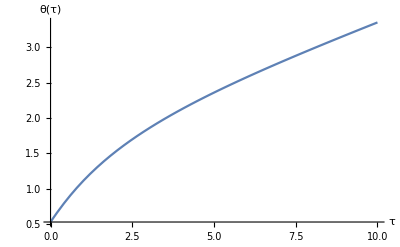

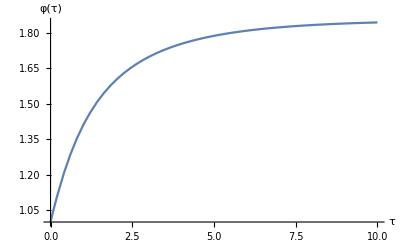

```mathematica
(* Redo this so plots are done on a surface... *) 

Plot[ ( θ[τ] /. thetaPhiSolutions[[1]]  ),{τ,0,10},AxesLabel->{τ,θ[τ]}]
Plot[ ( φ[τ] /. thetaPhiSolutions[[2]]  ),{τ,0,10},AxesLabel->{τ,φ[τ]}]
```